# Real Networks Analysis

## Definitions

```mathematica
<<IGraphM`
```

IGraph/M 0.4 (April 2, 2020)
Evaluate IGDocumentation[] to get started.

```mathematica
<<HypothesisTesting`
```

Finding Network Motifs:

```mathematica
NetMotFinderAllUp3[g_,e_]:=Module[{AR,gRands,real2NMFL,rands2NMFL,netMot2N,real3N,rands3N,netMot3N,allMotifs,uniqMotifs,uniqMotifs3N},
AR=Select[{{Graph[1->1],Length@Select[EdgeList[g],#[[1]]==#[[2]]&]}},#[[2]]>0&];
gRands=Table[IGRewire[g,1000000],100];
real2NMFL=Length@(Join@@(Select[Gather[Subgraph[g,#]&/@Union[Sort/@({1,2}/.IGLADFindSubisomorphisms[-Graphics-,g])],IsomorphicGraphQ[#1,#2]&],IsomorphicGraphQ[SimpleGraph[#[[1]]],-Graphics-]&]))//Quiet;
rands2NMFL=Length/@Table[Join@@Select[Gather[Subgraph[gRands[[i]],#]&/@Union[Sort/@({1,2}/.IGLADFindSubisomorphisms[-Graphics-,gRands[[i]]])],IsomorphicGraphQ[#1,#2]&],IsomorphicGraphQ[SimpleGraph[#[[1]]],-Graphics-]&],{i,1,Length@gRands}]//Quiet;
real3N=IGMotifs[g,3,1-e{1,1,1}];
rands3N=IGMotifs[#,3,1-e{1,1,1}]&/@gRands;
netMot2N=Select[{{-Graphics-,real2NMFL,N@((real2NMFL-Mean[rands2NMFL])/StandardDeviation[rands2NMFL])}},#[[3]]>(*3*)2&]//Quiet;netMot3N=SortBy[{#[[1]],#[[3]],N@((#[[3]]-Mean[#[[2]]])/StandardDeviation[#[[2]]])}&/@Select[Select[{IGData[{"AllDirectedGraphs",3}],rands3Nᵀ,real3N}ᵀ,WeaklyConnectedGraphQ[#[[1]]]&],N@((#[[3]]-Mean[#[[2]]])/StandardDeviation[#[[2]]])>(*3*)2&],-#[[3]]&]//Quiet;
allMotifs={AR,netMot2N,netMot3N};
allMotifs
]
```

Computing all possible circuit combinations for a pair of network motifs:

For a self-loop and other motifs:

```mathematica
circuitARComp[g_]:=Module[{gg,comps},
gg=DirectedEdge[{#[[1]],a},{#[[2]],a}]&/@(EdgeList@SimpleGraph[g]);
comps=Union[Graph/@((Join[EdgeList[gg],#]&/@Subsets[#->#&/@VertexList[gg],VertexCount[gg]])),SameTest->(IsomorphicGraphQ[#1,#2]&)];
comps]
```

For a pair of motifs (not including a self-loop):

```mathematica
circuitComp[g1_,g2_]:=Module[{gg1,gg2,rule,Jgraph,Jgraph2,comps,compsAll,nomOfC},
gg1=DirectedEdge[{#[[1]],a},{#[[2]],a}]&/@(EdgeList@g1);
gg2=DirectedEdge[{#[[1]],b},{#[[2]],b}]&/@(EdgeList@g2);
rule=Select[DeleteCases[Subsets[((Rule@@@Flatten[Table[{i,j},{i,VertexList[gg1]},{j,VertexList[gg2]}],1])),Min[VertexCount[g1],VertexCount[g2]]-1],{}],(Length[#]==Length[GatherBy[#,First]])&&(Length[#]==Length[GatherBy[#,Last]])&];
Jgraph={EdgeList[#[[1]]],#[[2]]}&/@(Gather[{Graph/@(Union[EdgeList@Graph[(Join@@(EdgeList/@{gg1,gg2}))/.#]]&/@rule),rule}ᵀ,IsomorphicGraphQ[#1[[1]],#2[[1]]]&][[;;,1]]);
Jgraph2=DeleteCases[Table[If[Select[Subgraph[Graph[Jgraph[[i,1]]],#]&/@(Range@VertexCount[g1]/.IGLADFindSubisomorphisms[g1,Graph[Jgraph[[i,1]]]]),IsomorphicGraphQ[#,g1]&]=={}||Select[Subgraph[Graph[Jgraph[[i,1]]],#]&/@(Range@VertexCount[g2]/.IGLADFindSubisomorphisms[g2,Graph[Jgraph[[i,1]]]]),IsomorphicGraphQ[#,g2]&]=={},{},Jgraph[[i]]],{i,1,Length@Jgraph}],{}];
nomOfC=Total@(3^(2Length[DeleteCases[Subsets[Complement[#[[1]],#[[2]]],{2}],{{_,x_},{_,x_}}]])&/@({VertexList[Graph[#[[1]]]],#[[2,;;,2]]}&/@Jgraph2));
Graph/@Jgraph2[[;;,1]]]
```

```mathematica
ExtComb[g_,g1_,g2_]:=Module[{gg1,gg2,rule,Jgraph,Jgraph2,Jgraph3,compsAll},
gg1=DirectedEdge[{#[[1]],a},{#[[2]],a}]&/@(EdgeList@g1);
gg2=DirectedEdge[{#[[1]],b},{#[[2]],b}]&/@(EdgeList@g2);
rule=Select[DeleteCases[Subsets[((Rule@@@Flatten[Table[{i,j},{i,VertexList[gg1]},{j,VertexList[gg2]}],1])),Min[VertexCount[g1],VertexCount[g2]]-1],{}],(Length[#]==Length[GatherBy[#,First]])&&(Length[#]==Length[GatherBy[#,Last]])&];
Jgraph={EdgeList[#[[1]]],#[[2]]}&/@(Gather[{Graph/@(Union[EdgeList@Graph[(Join@@(EdgeList/@{gg1,gg2}))/.#]]&/@rule),rule}ᵀ,IsomorphicGraphQ[#1[[1]],#2[[1]]]&][[;;,1]]);
Jgraph2=DeleteCases[Table[If[Select[Subgraph[Graph[Jgraph[[i,1]]],#]&/@(Range@VertexCount[g1]/.IGLADFindSubisomorphisms[g1,Graph[Jgraph[[i,1]]]]),IsomorphicGraphQ[#,g1]&]=={}||Select[Subgraph[Graph[Jgraph[[i,1]]],#]&/@(Range@VertexCount[g2]/.IGLADFindSubisomorphisms[g2,Graph[Jgraph[[i,1]]]]),IsomorphicGraphQ[#,g2]&]=={},{},Jgraph[[i]]],{i,1,Length@Jgraph}],{}];
Jgraph3=Select[Jgraph2,IsomorphicGraphQ[g,Graph[#[[1]]]]&];compsAll=Union[Join@@(Graph/@(Join@@@Thread[#,List,{2}])&/@({Jgraph3[[;;,1]],Subsets[DirectedEdge@@@Join[#,Reverse/@#],(VertexCount[g1]+VertexCount[g2]-2)2]&@DeleteCases[Subsets[Complement[#[[1]],#[[2]]],{2}],{{_,x_},{_,x_}}]&/@({VertexList[Graph[#[[1]]]],#[[2,;;,2]]}&/@Jgraph3)}ᵀ)),SameTest->(IsomorphicGraphQ[#1,#2]&)];
compsAll]
```

Motif Dictionary:

```mathematica
md=Join[Graph/@{{1->1},{1->2,2->1}},Select[IGData[{"AllDirectedGraphs",3}],WeaklyConnectedGraphQ[#]&]];
```

Finding significantly enriched and under-represented motif combinations of one shared node:

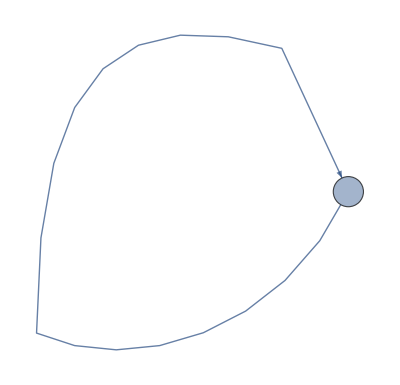
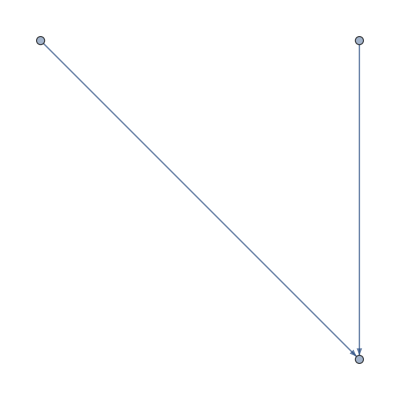
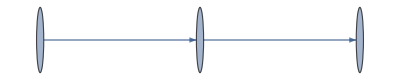
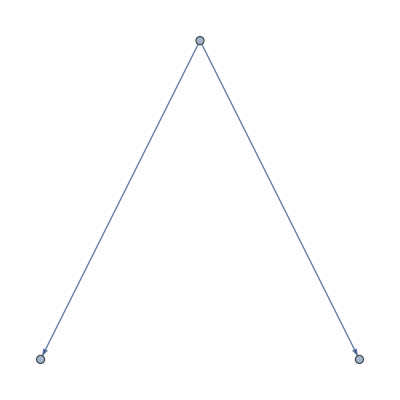
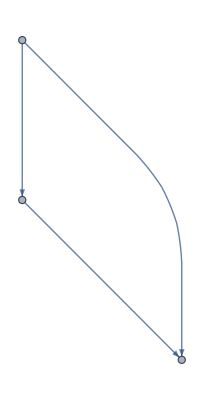

```mathematica
EnrichedCombsMFinderRandUpTo3[g_,gRands_,netMot_,pos_]:=Module[{allMotifsIns,allMotifsInsRand,ARNodes,MFL2Nodes,regted3InNodes,regted3OutNodes,chain3InNodes,chain3MedNodes,chain3OutNodes,in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes,reging3InNodes,reging3OutNodes,FFL3InNodes,FFL3MedNodes,FFL3OutNodes,RegtedMFL3InNodes,RegtedMFL3OutNodes,out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes,FBL3Nodes,LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes,RegingMFL3InNodes,RegingMFL3OutNodes,DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes,ARNodesRand,MFL2NodesRand,regted3InNodesRand,regted3OutNodesRand,chain3InNodesRand,chain3MedNodesRand,chain3OutNodesRand,in1MFL3InNodesRand,in1MFL3Out1NodesRand,in1MFL3Out2NodesRand,reging3InNodesRand,reging3OutNodesRand,FFL3InNodesRand,FFL3MedNodesRand,FFL3OutNodesRand,RegtedMFL3InNodesRand,RegtedMFL3OutNodesRand,out1MFL3In1NodesRand,out1MFL3In2NodesRand,out1MFL3OutNodesRand,FBL3NodesRand,LoopMFL3InNodesRand,LoopMFL3MedNodesRand,LoopMFL3OutNodesRand,RegingMFL3InNodesRand,RegingMFL3OutNodesRand,DoubleMFL3InNodesRand,DoubleMFL3OutNodesRand,DoubleMFL3ConnNodesRand,allregted3s,allregted3sRand,allChain3s,allChain3sRand,allIn1MFL3s,allIn1MFL3sRand,allFFL3s,allFFL3sRand,allreging3s,allreging3sRand,allRegtedMFL3s,allRegtedMFL3sRand,allOut1MFL3s,allOut1MFL3sRand,allLoopMFL3s,allLoopMFL3sRand,allRegingMFL3s,allRegingMFL3sRand,allDoubleMFL3s,allDoubleMFL3sRand,TwoMFL3SideNodes,TwoMFL3MidNodes,TwoMFL3SideNodesRand,TwoMFL3MidNodesRand,allTwoMFL3s,allTwoMFL3sRand,ThreeMFL3Nodes,ThreeMFL3NodesRand,motifsRoles,motifsRoles2,sameRoleCombs,sameRoleCombs2,nodesInMotifRoles,nodesInMotifRolesRand,motifCombs,motifCombsSame,cols,bg,t},
allMotifsIns=DeleteCases[Prepend[Table[Select[Subgraph[SimpleGraph[g],#]&/@Union[Sort/@((Range@VertexCount[motif])/.IGLADFindSubisomorphisms[motif,SimpleGraph[g]])],IsomorphicGraphQ[SimpleGraph[#],motif]&],{motif,Select[netMot,-Graphics-≠ #&]}],Select[Subgraph[g,#]&/@Union[Sort/@((Range@VertexCount[-Graphics-])/.IGLADFindSubisomorphisms[-Graphics-,g])],IsomorphicGraphQ[#,-Graphics-]&]],{}];
allMotifsInsRand=Table[Table[Select[Subgraph[SimpleGraph[gRands[[i]]],#]&/@Union[Sort/@((Range@VertexCount[motif])/.IGLADFindSubisomorphisms[motif,SimpleGraph[gRands[[i]]]])],IsomorphicGraphQ[SimpleGraph[#],motif]&],{motif,Select[netMot,-Graphics-≠ #&]}],{i,1,Length@gRands}];
ARNodes={#,1}&/@Select[EdgeList[g],#[[1]]==#[[2]]&][[;;,1]];
ARNodesRand=Table[{#,1}&/@RandomChoice[VertexList[gRands[[i]]],Length@ARNodes],{i,1,Length@gRands}];
MFL2Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
MFL2NodesRand=Table[Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
allregted3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allregted3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
regted3InNodes=Tally[Flatten[#[[;;,1]]&/@(EdgeList/@(Join@@allregted3s))]];
regted3OutNodes=Tally[#[[1,2]]&/@(EdgeList/@(Join@@allregted3s))];
regted3InNodesRand=Table[Tally[Flatten[#[[;;,1]]&/@EdgeList/@(Join@@allregted3sRand[[i]])]],{i,1,Length@gRands}];
regted3OutNodesRand=Table[Tally[#[[1,2]]&/@EdgeList/@(Join@@allregted3sRand[[i]])],{i,1,Length@gRands}];
allChain3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allChain3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
chain3InNodes=Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,2]]][[1]]&/@EdgeList/@(Join@@allChain3s)];
chain3MedNodes=Tally[Select[Tally[Flatten[{#[[;;,1]],#[[;;,2]]},1]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allChain3s)];
chain3OutNodes=Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,1]]][[1]]&/@EdgeList/@(Join@@allChain3s)];
chain3InNodesRand=Table[Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,2]]][[1]]&/@EdgeList/@(Join@@allChain3sRand[[i]])],{i,1,Length@gRands}];
chain3MedNodesRand=Table[Tally[Select[Tally[Flatten[{#[[;;,1]],#[[;;,2]]},1]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allChain3sRand[[i]])],{i,1,Length@gRands}];
chain3OutNodesRand=Table[Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,1]]][[1]]&/@EdgeList/@(Join@@allChain3sRand[[i]])],{i,1,Length@gRands}];
allIn1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allIn1MFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
in1MFL3InNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3Out1Nodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3Out2Nodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3InNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]])],{i,1,Length@gRands}];
in1MFL3Out1NodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]])],{i,1,Length@gRands}];
in1MFL3Out2NodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]])],{i,1,Length@gRands}];
allreging3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allreging3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
reging3InNodes=Tally[#[[1,1]]&/@(EdgeList/@(Join@@allreging3s))];
reging3OutNodes=Tally[Flatten[#[[;;,2]]&/@(EdgeList/@(Join@@allreging3s))]];
reging3InNodesRand=Table[Tally[#[[1,1]]&/@EdgeList/@(Join@@allreging3sRand[[i]])],{i,1,Length@gRands}];
reging3OutNodesRand=Table[Tally[Flatten[#[[;;,2]]&/@EdgeList/@(Join@@allreging3sRand[[i]])]],{i,1,Length@gRands}];
allFFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allFFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
FFL3InNodes=Tally[(Select[Tally[#[[;;,1]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3MedNodes=Tally[(Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3OutNodes=Tally[(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3InNodesRand=Table[Tally[(Select[Tally[#[[;;,1]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]]],{i,1,Length@gRands}];
FFL3MedNodesRand=Table[Tally[(Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]]],{i,1,Length@gRands}];
FFL3OutNodesRand=Table[Tally[(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]]],{i,1,Length@gRands}];
allRegtedMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allRegtedMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
RegtedMFL3InNodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegtedMFL3s)];
RegtedMFL3OutNodes=Tally[Flatten[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegtedMFL3s)]];
RegtedMFL3InNodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegtedMFL3sRand[[i]])],{i,1,Length@gRands}];
RegtedMFL3OutNodesRand=Table[Tally[Flatten[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegtedMFL3sRand[[i]])]],{i,1,Length@gRands}];
allOut1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allOut1MFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
out1MFL3In1Nodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3In2Nodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3OutNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3In1NodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]])],{i,1,Length@gRands}];
out1MFL3In2NodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]])],{i,1,Length@gRands}];
out1MFL3OutNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]])],{i,1,Length@gRands}];
allTwoMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allTwoMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
TwoMFL3SideNodes=Tally[Flatten[Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@EdgeList/@(Join@@allTwoMFL3s)]];
TwoMFL3MidNodes=Tally[Select[Tally[#[[;;,1]]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allTwoMFL3s)];
TwoMFL3SideNodesRand=Table[Tally[Flatten[Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@EdgeList/@(Join@@allTwoMFL3sRand[[i]])]],{i,1,Length@gRands}];
TwoMFL3MidNodesRand=Table[Tally[Select[Tally[#[[;;,1]]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allTwoMFL3sRand[[i]])],{i,1,Length@gRands}];
FBL3Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
FBL3NodesRand=Table[Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
allLoopMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allLoopMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
LoopMFL3InNodes=Tally[Select[Tally[(#[[1]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3MedNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3OutNodes=Tally[Select[Tally[(#[[2]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3InNodesRand=Table[Tally[Select[Tally[(#[[1]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]])],{i,1,Length@gRands}];
LoopMFL3MedNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]])],{i,1,Length@gRands}];
LoopMFL3OutNodesRand=Table[Tally[Select[Tally[(#[[2]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]])],{i,1,Length@gRands}];
allRegingMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allRegingMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
RegingMFL3InNodes=Tally[Flatten[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegingMFL3s)]];
RegingMFL3OutNodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegingMFL3s)];
RegingMFL3InNodesRand=Table[Tally[Flatten[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegingMFL3sRand[[i]])]],{i,1,Length@gRands}];
RegingMFL3OutNodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegingMFL3sRand[[i]])],{i,1,Length@gRands}];
allDoubleMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allDoubleMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
DoubleMFL3InNodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3OutNodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3ConnNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==4&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3InNodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]])],{i,1,Length@gRands}];
DoubleMFL3OutNodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]])],{i,1,Length@gRands}];
DoubleMFL3ConnNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==4&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]])],{i,1,Length@gRands}];
ThreeMFL3Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
ThreeMFL3NodesRand=Table[Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
motifsRoles={{{{a1->a1},a1}},{{{b1->b2,b2->b1},b1}},{{{y1->y2,y3->y2},y1},{{z1->z2,z3->z2},z2}},{{{g1->g2,g2->g3},g1},{{h1->h2,h2->h3},h2},{{i1->i2,i2->i3},i3}},{{{j1->j3,j2->j3,j3->j2},j1},{{k1->k3,k2->k3,k3->k2},k3},{{l1->l3,l2->l3,l3->l2},l2}},{{{t1->t2,t1->t3},t1},{{x1->x2,x1->x3},x2}},{{{c1->c2,c1->c3,c2->c3},c1},{{d1->d2,d1->d3,d2->d3},d2},{{e1->e2,e1->e3,e2->e3},e3}},{{{m1->m3,m2->m1,m2->m3,m3->m1},m2},{{n1->n3,n2->n1,n2->n3,n3->n1},n1}},{{{o2->o3,o3->o1,o3->o2},o3},{{p2->p3,p3->p1,p3->p2},p2},{{q2->q3,q3->q1,q3->q2},q1}},{{{dd1->dd2,dd2->dd1,dd2->dd3,dd3->dd2},dd1},{{ee1->ee2,ee2->ee1,ee2->ee3,ee3->ee2},ee2}},{{{f1->f2,f2->f3,f3->f1},f1}},{{{r1->r3,r2->r1,r3->r1,r3->r2},r3},{{s1->s3,s2->s1,s3->s1,s3->s2},s2},{{w1->w3,w2->w1,w3->w1,w3->w2},w1}},{{{y2->y1,y2->y3,y3->y1,y3->y2},y2},{{z2->z1,z2->z3,z3->z1,z3->z2},z1}},{{{aa1->aa3,aa2->aa1,aa2->aa3,aa3->aa1,aa3->aa2},aa2},{{bb1->bb3,bb2->bb1,bb2->bb3,bb3->bb1,bb3->bb2},bb1},{{cc1->cc3,cc2->cc1,cc2->cc3,cc3->cc1,cc3->cc2},cc3}},{{{ff1->ff2,ff2->ff1,ff2->ff3,ff3->ff2,ff3->ff1,ff1->ff3},ff1}}};
motifsRoles2=Flatten[motifsRoles[[pos]],1](*Select[motifsRoles,Or@@Table[IsomorphicGraphQ[nm,AdjacencyGraph[AdjacencyMatrix[#[[1]]],DirectedEdges->True]],{nm,netMot}]&]*);
sameRoleCombs=Map[Graph[#,DirectedEdges->True]&,{{{1->1}},{{1->2,2->1,2->3,3->2}},{{1->2,3->2,3->4,5->4},{1->2,3->2,4->2,5->2}},{{1->2,2->3,1->4,4->5},{1->2,2->3,4->2,2->5},{1->2,2->3,4->5,5->3}},{{1->2,2->3,3->2,1->4,4->5,5->4},{1->2,2->3,3->2,4->2,2->5,5->2},{1->2,2->3,3->2,3->5,5->3,4->5}},{{1->2,1->3,1->4,1->5},{1->2,1->3,4->2,4->5}},{{1->2,1->3,2->3,1->4,1->5,4->5},{1->2,1->3,2->3,4->2,4->5,2->5},{1->2,1->3,2->3,4->5,4->3,5->3}},{{1->2,1->3,2->3,3->2,1->4,1->5,4->5,5->4},{1->2,1->3,2->3,3->2,5->3,5->4,3->4,4->3}},{{1->2,2->1,1->3,1->5,1->4,4->1},{1->2,2->1,2->5,1->3,3->1,3->4},{1->2,2->1,2->3,4->5,5->4,5->3}},{{1->2,2->1,2->3,3->2,1->4,4->1,4->5,5->4},{1->2,2->1,2->3,3->2,2->4,4->2,2->5,5->2}},{{1->2,2->3,3->1,1->4,4->5,5->1}},{{1->2,2->1,1->3,3->2,1->5,5->4,4->1,1->4},{1->3,3->2,2->3,2->1,1->5,5->4,4->5,4->1},{1->2,2->1,2->3,3->1,1->5,5->1,5->4,4->1}},{{1->2,2->1,1->4,2->4,2->3,3->2,2->5,3->5},{2->3,3->2,4->5,5->4,2->1,3->1,4->1,5->1}},{{1->2,2->1,2->3,3->2,1->3,1->4,4->5,5->4,1->5,5->1},{1->2,2->1,2->3,3->2,3->1,1->4,4->1,5->4,4->5,5->1},{1->2,2->1,1->5,5->1,1->3,3->1,1->4,4->1,4->5,3->2}},{{1->2,2->1,2->3,3->2,3->1,1->3,1->4,4->1,4->5,5->4,5->1,1->5}}},{2}];
sameRoleCombs2=Flatten[sameRoleCombs[[pos]],1];
nodesInMotifRoles=DeleteCases[{ARNodes,MFL2Nodes,regted3InNodes,regted3OutNodes,chain3InNodes,chain3MedNodes,chain3OutNodes,in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes,reging3InNodes,reging3OutNodes,FFL3InNodes,FFL3MedNodes,FFL3OutNodes,RegtedMFL3InNodes,RegtedMFL3OutNodes,out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes,TwoMFL3SideNodes,TwoMFL3MidNodes,FBL3Nodes,LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes,RegingMFL3InNodes,RegingMFL3OutNodes,DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes,ThreeMFL3Nodes},{}];
nodesInMotifRolesRand=Select[{ARNodesRand,MFL2NodesRand,regted3InNodesRand,regted3OutNodesRand,chain3InNodesRand,chain3MedNodesRand,chain3OutNodesRand,in1MFL3InNodesRand,in1MFL3Out1NodesRand,in1MFL3Out2NodesRand,reging3InNodesRand,reging3OutNodesRand,FFL3InNodesRand,FFL3MedNodesRand,FFL3OutNodesRand,RegtedMFL3InNodesRand,RegtedMFL3OutNodesRand,out1MFL3In1NodesRand,out1MFL3In2NodesRand,out1MFL3OutNodesRand,TwoMFL3SideNodesRand,TwoMFL3MidNodesRand,FBL3NodesRand,LoopMFL3InNodesRand,LoopMFL3MedNodesRand,LoopMFL3OutNodesRand,RegingMFL3InNodesRand,RegingMFL3OutNodesRand,DoubleMFL3InNodesRand,DoubleMFL3OutNodesRand,DoubleMFL3ConnNodesRand,ThreeMFL3NodesRand},Union[#]≠{{}}&]ᵀ;
motifCombs={(N@(Length[Intersection[#[[1]],#[[2]]]]/Length[Union[#[[1]],#[[2]]]])&/@Subsets[nodesInMotifRoles[[;;,;;,1]],{2}])/.Indeterminate->0,((N@(Length[Intersection[#[[1]],#[[2]]]]/Length[Union[#[[1]],#[[2]]]])&/@Subsets[#[[;;,;;,1]],{2}]&/@nodesInMotifRolesRand)ᵀ)/.Indeterminate->0,Table[Graph[(Join@@motifsRoles2[[i,1]])/.motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]],DirectedEdges->True],{i,Subsets[Range@Length[motifsRoles2],{2}]}]}ᵀ;
motifCombsSame={(N@(Count[#,_?(#[[2]]>1&)]/Length[#])&/@nodesInMotifRoles)/.Indeterminate->0,(Map[N@(Count[#,_?(#[[2]]>1&)]/Length[#])&,nodesInMotifRolesRand,{2}]ᵀ)/.Indeterminate->0,sameRoleCombs2}ᵀ;
cols=ColorData["TemperatureMap"][#]&/@Rescale[(((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@(Join@@{motifCombs,motifCombsSame}))/.Indeterminate->0/.ComplexInfinity->0//Quiet)];
bg=ConstantArray[White,{Length[sameRoleCombs2]+1,Length[sameRoleCombs2]+1}];
Table[bg[[i+1,i+2;;]]=cols[[Length[sameRoleCombs2] i-Total[Range@i]-(Length[sameRoleCombs2]-1-i);;Length[sameRoleCombs2] i-Total[Range@i]]],{i,1,Length[sameRoleCombs2]-1}];
Table[bg[[i+1,i+1]]=cols[[i+Length[sameRoleCombs2] (Length[sameRoleCombs2]-1)-Total[Range@(Length[sameRoleCombs2]-1)]]],{i,1,Length[sameRoleCombs2]}];
t=ConstantArray["",{Length[sameRoleCombs2]+1,Length[sameRoleCombs2]+1}];
t[[1,2;;]]=HighlightGraph[#[[1]],#[[2]],VertexSize->0.07]&/@motifsRoles2;
Table[t[[i,1]]=HighlightGraph[#[[1]],#[[2]],VertexSize->0.07]&@motifsRoles2[[i-1]],{i,2,Length[sameRoleCombs2]+1}];
Table[t[[i+1,i+2;;]]=Table[Graph[(Join@@motifsRoles2[[i,1]])/.motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]],DirectedEdges->True],{i,Subsets[Range@(Length[sameRoleCombs2]),{2}]}][[Length[sameRoleCombs2] i-Total[Range@i]-(Length[sameRoleCombs2]-1-i);;Length[sameRoleCombs2] i-Total[Range@i]]],{i,1,Length[sameRoleCombs2]-1}];
Table[t[[i+1,i+1]]=sameRoleCombs2[[i]],{i,1,Length[sameRoleCombs2]}];
{Join@@{motifCombs,motifCombsSame},{(Join@@{motifCombs,motifCombsSame})[[#[[1]],-1]],((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&@(Join@@{motifCombs,motifCombsSame})[[#[[1]]]]),#[[3]]}&/@Select[{#[[1,1]],#[[1,2]],(#[[2]])/Length[(Join@@{motifCombs,motifCombsSame})] 0.05,#[[1,3]]}&/@({SortBy[Table[{i,NormalPValue[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&@(Join@@{motifCombs,motifCombsSame})[[i]])][[2]],(Join@@{motifCombs,motifCombsSame})[[i,1]]},{i,1,Length[(Join@@{motifCombs,motifCombsSame})]}],#[[2]]&],Range@Length[(Join@@{motifCombs,motifCombsSame})]}ᵀ),#[[2]]≤#[[3]]&&#[[4]]≥0.15&]//Quiet,BarLegend[{"TemperatureMap",{Min[#],Max[#]}&@(((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@(Join@@{motifCombs,motifCombsSame}))/.Indeterminate->0/.ComplexInfinity->0//Quiet)}],Grid[t,Frame->All,Background->{None,None,Thread[Complement[Join@@Table[{i,j},{i,1,Length[sameRoleCombs2]+1},{j,1,Length[sameRoleCombs2]+1}],Position[bg,White]]->DeleteCases[Flatten[bg,1],White]]}]}
]
```

Finding significantly enriched and under-represented motif combinations of one shared node (when the random networks are already provided with autoregulation):

```mathematica
EnrichedCombsMFinderRand2UpTo3[g_,gRands_,netMot_,pos_]:=Module[{allMotifsIns,allMotifsInsRand,ARNodes,MFL2Nodes,regted3InNodes,regted3OutNodes,chain3InNodes,chain3MedNodes,chain3OutNodes,in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes,reging3InNodes,reging3OutNodes,FFL3InNodes,FFL3MedNodes,FFL3OutNodes,RegtedMFL3InNodes,RegtedMFL3OutNodes,out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes,FBL3Nodes,LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes,RegingMFL3InNodes,RegingMFL3OutNodes,DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes,ARNodesRand,MFL2NodesRand,regted3InNodesRand,regted3OutNodesRand,chain3InNodesRand,chain3MedNodesRand,chain3OutNodesRand,in1MFL3InNodesRand,in1MFL3Out1NodesRand,in1MFL3Out2NodesRand,reging3InNodesRand,reging3OutNodesRand,FFL3InNodesRand,FFL3MedNodesRand,FFL3OutNodesRand,RegtedMFL3InNodesRand,RegtedMFL3OutNodesRand,out1MFL3In1NodesRand,out1MFL3In2NodesRand,out1MFL3OutNodesRand,FBL3NodesRand,LoopMFL3InNodesRand,LoopMFL3MedNodesRand,LoopMFL3OutNodesRand,RegingMFL3InNodesRand,RegingMFL3OutNodesRand,DoubleMFL3InNodesRand,DoubleMFL3OutNodesRand,DoubleMFL3ConnNodesRand,allregted3s,allregted3sRand,allChain3s,allChain3sRand,allIn1MFL3s,allIn1MFL3sRand,allFFL3s,allFFL3sRand,allreging3s,allreging3sRand,allRegtedMFL3s,allRegtedMFL3sRand,allOut1MFL3s,allOut1MFL3sRand,allLoopMFL3s,allLoopMFL3sRand,allRegingMFL3s,allRegingMFL3sRand,allDoubleMFL3s,allDoubleMFL3sRand,TwoMFL3SideNodes,TwoMFL3MidNodes,TwoMFL3SideNodesRand,TwoMFL3MidNodesRand,allTwoMFL3s,allTwoMFL3sRand,ThreeMFL3Nodes,ThreeMFL3NodesRand,motifsRoles,motifsRoles2,sameRoleCombs,sameRoleCombs2,nodesInMotifRoles,nodesInMotifRolesRand,motifCombs,motifCombsSame,cols,bg,t},
allMotifsIns=DeleteCases[Prepend[Table[Select[Subgraph[SimpleGraph[g],#]&/@Union[Sort/@((Range@VertexCount[motif])/.IGLADFindSubisomorphisms[motif,SimpleGraph[g]])],IsomorphicGraphQ[SimpleGraph[#],motif]&],{motif,Select[netMot,-Graphics-≠ #&]}],Select[Subgraph[g,#]&/@Union[Sort/@((Range@VertexCount[-Graphics-])/.IGLADFindSubisomorphisms[-Graphics-,g])],IsomorphicGraphQ[#,-Graphics-]&]],{}];
allMotifsInsRand=Table[Table[Select[Subgraph[SimpleGraph[gRands[[i]]],#]&/@Union[Sort/@((Range@VertexCount[motif])/.IGLADFindSubisomorphisms[motif,SimpleGraph[gRands[[i]]]])],IsomorphicGraphQ[SimpleGraph[#],motif]&],{motif,Select[netMot,-Graphics-≠ #&]}],{i,1,Length@gRands}];
ARNodes={#,1}&/@Select[EdgeList[g],#[[1]]==#[[2]]&][[;;,1]];
ARNodesRand=Table[{#,1}&/@Select[EdgeList[gRands[[i]]],#[[1]]==#[[2]]&][[;;,1]],{i,1,Length@gRands}];
MFL2Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
MFL2NodesRand=Table[Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
allregted3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allregted3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
regted3InNodes=Tally[Flatten[#[[;;,1]]&/@(EdgeList/@(Join@@allregted3s))]];
regted3OutNodes=Tally[#[[1,2]]&/@(EdgeList/@(Join@@allregted3s))];
regted3InNodesRand=Table[Tally[Flatten[#[[;;,1]]&/@EdgeList/@(Join@@allregted3sRand[[i]])]],{i,1,Length@gRands}];
regted3OutNodesRand=Table[Tally[#[[1,2]]&/@EdgeList/@(Join@@allregted3sRand[[i]])],{i,1,Length@gRands}];
allChain3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allChain3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
chain3InNodes=Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,2]]][[1]]&/@EdgeList/@(Join@@allChain3s)];
chain3MedNodes=Tally[Select[Tally[Flatten[{#[[;;,1]],#[[;;,2]]},1]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allChain3s)];
chain3OutNodes=Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,1]]][[1]]&/@EdgeList/@(Join@@allChain3s)];
chain3InNodesRand=Table[Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,2]]][[1]]&/@EdgeList/@(Join@@allChain3sRand[[i]])],{i,1,Length@gRands}];
chain3MedNodesRand=Table[Tally[Select[Tally[Flatten[{#[[;;,1]],#[[;;,2]]},1]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allChain3sRand[[i]])],{i,1,Length@gRands}];
chain3OutNodesRand=Table[Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,1]]][[1]]&/@EdgeList/@(Join@@allChain3sRand[[i]])],{i,1,Length@gRands}];
allIn1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allIn1MFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
in1MFL3InNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3Out1Nodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3Out2Nodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3InNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]])],{i,1,Length@gRands}];
in1MFL3Out1NodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]])],{i,1,Length@gRands}];
in1MFL3Out2NodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]])],{i,1,Length@gRands}];
allreging3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allreging3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
reging3InNodes=Tally[#[[1,1]]&/@(EdgeList/@(Join@@allreging3s))];
reging3OutNodes=Tally[Flatten[#[[;;,2]]&/@(EdgeList/@(Join@@allreging3s))]];
reging3InNodesRand=Table[Tally[#[[1,1]]&/@EdgeList/@(Join@@allreging3sRand[[i]])],{i,1,Length@gRands}];
reging3OutNodesRand=Table[Tally[Flatten[#[[;;,2]]&/@EdgeList/@(Join@@allreging3sRand[[i]])]],{i,1,Length@gRands}];
allFFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allFFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
FFL3InNodes=Tally[(Select[Tally[#[[;;,1]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3MedNodes=Tally[(Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3OutNodes=Tally[(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3InNodesRand=Table[Tally[(Select[Tally[#[[;;,1]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]]],{i,1,Length@gRands}];
FFL3MedNodesRand=Table[Tally[(Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]]],{i,1,Length@gRands}];
FFL3OutNodesRand=Table[Tally[(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]]],{i,1,Length@gRands}];
allRegtedMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allRegtedMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
RegtedMFL3InNodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegtedMFL3s)];
RegtedMFL3OutNodes=Tally[Flatten[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegtedMFL3s)]];
RegtedMFL3InNodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegtedMFL3sRand[[i]])],{i,1,Length@gRands}];
RegtedMFL3OutNodesRand=Table[Tally[Flatten[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegtedMFL3sRand[[i]])]],{i,1,Length@gRands}];
allOut1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allOut1MFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
out1MFL3In1Nodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3In2Nodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3OutNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3In1NodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]])],{i,1,Length@gRands}];
out1MFL3In2NodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]])],{i,1,Length@gRands}];
out1MFL3OutNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]])],{i,1,Length@gRands}];
allTwoMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allTwoMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
TwoMFL3SideNodes=Tally[Flatten[Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@EdgeList/@(Join@@allTwoMFL3s)]];
TwoMFL3MidNodes=Tally[Select[Tally[#[[;;,1]]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allTwoMFL3s)];
TwoMFL3SideNodesRand=Table[Tally[Flatten[Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@EdgeList/@(Join@@allTwoMFL3sRand[[i]])]],{i,1,Length@gRands}];
TwoMFL3MidNodesRand=Table[Tally[Select[Tally[#[[;;,1]]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allTwoMFL3sRand[[i]])],{i,1,Length@gRands}];
FBL3Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
FBL3NodesRand=Table[Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
allLoopMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allLoopMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
LoopMFL3InNodes=Tally[Select[Tally[(#[[1]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3MedNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3OutNodes=Tally[Select[Tally[(#[[2]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3InNodesRand=Table[Tally[Select[Tally[(#[[1]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]])],{i,1,Length@gRands}];
LoopMFL3MedNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]])],{i,1,Length@gRands}];
LoopMFL3OutNodesRand=Table[Tally[Select[Tally[(#[[2]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]])],{i,1,Length@gRands}];
allRegingMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allRegingMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
RegingMFL3InNodes=Tally[Flatten[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegingMFL3s)]];
RegingMFL3OutNodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegingMFL3s)];
RegingMFL3InNodesRand=Table[Tally[Flatten[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegingMFL3sRand[[i]])]],{i,1,Length@gRands}];
RegingMFL3OutNodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegingMFL3sRand[[i]])],{i,1,Length@gRands}];
allDoubleMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allDoubleMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
DoubleMFL3InNodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3OutNodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3ConnNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==4&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3InNodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]])],{i,1,Length@gRands}];
DoubleMFL3OutNodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]])],{i,1,Length@gRands}];
DoubleMFL3ConnNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==4&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]])],{i,1,Length@gRands}];
ThreeMFL3Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
ThreeMFL3NodesRand=Table[Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
motifsRoles={{{{a1->a1},a1}},{{{b1->b2,b2->b1},b1}},{{{y1->y2,y3->y2},y1},{{z1->z2,z3->z2},z2}},{{{g1->g2,g2->g3},g1},{{h1->h2,h2->h3},h2},{{i1->i2,i2->i3},i3}},{{{j1->j3,j2->j3,j3->j2},j1},{{k1->k3,k2->k3,k3->k2},k3},{{l1->l3,l2->l3,l3->l2},l2}},{{{t1->t2,t1->t3},t1},{{x1->x2,x1->x3},x2}},{{{c1->c2,c1->c3,c2->c3},c1},{{d1->d2,d1->d3,d2->d3},d2},{{e1->e2,e1->e3,e2->e3},e3}},{{{m1->m3,m2->m1,m2->m3,m3->m1},m2},{{n1->n3,n2->n1,n2->n3,n3->n1},n1}},{{{o2->o3,o3->o1,o3->o2},o3},{{p2->p3,p3->p1,p3->p2},p2},{{q2->q3,q3->q1,q3->q2},q1}},{{{dd1->dd2,dd2->dd1,dd2->dd3,dd3->dd2},dd1},{{ee1->ee2,ee2->ee1,ee2->ee3,ee3->ee2},ee2}},{{{f1->f2,f2->f3,f3->f1},f1}},{{{r1->r3,r2->r1,r3->r1,r3->r2},r3},{{s1->s3,s2->s1,s3->s1,s3->s2},s2},{{w1->w3,w2->w1,w3->w1,w3->w2},w1}},{{{y2->y1,y2->y3,y3->y1,y3->y2},y2},{{z2->z1,z2->z3,z3->z1,z3->z2},z1}},{{{aa1->aa3,aa2->aa1,aa2->aa3,aa3->aa1,aa3->aa2},aa2},{{bb1->bb3,bb2->bb1,bb2->bb3,bb3->bb1,bb3->bb2},bb1},{{cc1->cc3,cc2->cc1,cc2->cc3,cc3->cc1,cc3->cc2},cc3}},{{{ff1->ff2,ff2->ff1,ff2->ff3,ff3->ff2,ff3->ff1,ff1->ff3},ff1}}};
motifsRoles2=Flatten[motifsRoles[[pos]],1];
sameRoleCombs=Map[Graph[#,DirectedEdges->True]&,{{{1->1}},{{1->2,2->1,2->3,3->2}},{{1->2,3->2,3->4,5->4},{1->2,3->2,4->2,5->2}},{{1->2,2->3,1->4,4->5},{1->2,2->3,4->2,2->5},{1->2,2->3,4->5,5->3}},{{1->2,2->3,3->2,1->4,4->5,5->4},{1->2,2->3,3->2,4->2,2->5,5->2},{1->2,2->3,3->2,3->5,5->3,4->5}},{{1->2,1->3,1->4,1->5},{1->2,1->3,4->2,4->5}},{{1->2,1->3,2->3,1->4,1->5,4->5},{1->2,1->3,2->3,4->2,4->5,2->5},{1->2,1->3,2->3,4->5,4->3,5->3}},{{1->2,1->3,2->3,3->2,1->4,1->5,4->5,5->4},{1->2,1->3,2->3,3->2,5->3,5->4,3->4,4->3}},{{1->2,2->1,1->3,1->5,1->4,4->1},{1->2,2->1,2->5,1->3,3->1,3->4},{1->2,2->1,2->3,4->5,5->4,5->3}},{{1->2,2->1,2->3,3->2,1->4,4->1,4->5,5->4},{1->2,2->1,2->3,3->2,2->4,4->2,2->5,5->2}},{{1->2,2->3,3->1,1->4,4->5,5->1}},{{1->2,2->1,1->3,3->2,1->5,5->4,4->1,1->4},{1->3,3->2,2->3,2->1,1->5,5->4,4->5,4->1},{1->2,2->1,2->3,3->1,1->5,5->1,5->4,4->1}},{{1->2,2->1,1->4,2->4,2->3,3->2,2->5,3->5},{2->3,3->2,4->5,5->4,2->1,3->1,4->1,5->1}},{{1->2,2->1,2->3,3->2,1->3,1->4,4->5,5->4,1->5,5->1},{1->2,2->1,2->3,3->2,3->1,1->4,4->1,5->4,4->5,5->1},{1->2,2->1,1->5,5->1,1->3,3->1,1->4,4->1,4->5,3->2}},{{1->2,2->1,2->3,3->2,3->1,1->3,1->4,4->1,4->5,5->4,5->1,1->5}}},{2}];
sameRoleCombs2=Flatten[sameRoleCombs[[pos]],1];
nodesInMotifRoles=DeleteCases[{ARNodes,MFL2Nodes,regted3InNodes,regted3OutNodes,chain3InNodes,chain3MedNodes,chain3OutNodes,in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes,reging3InNodes,reging3OutNodes,FFL3InNodes,FFL3MedNodes,FFL3OutNodes,RegtedMFL3InNodes,RegtedMFL3OutNodes,out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes,TwoMFL3SideNodes,TwoMFL3MidNodes,FBL3Nodes,LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes,RegingMFL3InNodes,RegingMFL3OutNodes,DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes,ThreeMFL3Nodes},{}];
nodesInMotifRolesRand=Select[{ARNodesRand,MFL2NodesRand,regted3InNodesRand,regted3OutNodesRand,chain3InNodesRand,chain3MedNodesRand,chain3OutNodesRand,in1MFL3InNodesRand,in1MFL3Out1NodesRand,in1MFL3Out2NodesRand,reging3InNodesRand,reging3OutNodesRand,FFL3InNodesRand,FFL3MedNodesRand,FFL3OutNodesRand,RegtedMFL3InNodesRand,RegtedMFL3OutNodesRand,out1MFL3In1NodesRand,out1MFL3In2NodesRand,out1MFL3OutNodesRand,TwoMFL3SideNodesRand,TwoMFL3MidNodesRand,FBL3NodesRand,LoopMFL3InNodesRand,LoopMFL3MedNodesRand,LoopMFL3OutNodesRand,RegingMFL3InNodesRand,RegingMFL3OutNodesRand,DoubleMFL3InNodesRand,DoubleMFL3OutNodesRand,DoubleMFL3ConnNodesRand,ThreeMFL3NodesRand},Union[#]≠{{}}&]ᵀ;
motifCombs={(N@(Length[Intersection[#[[1]],#[[2]]]]/Length[Union[#[[1]],#[[2]]]])&/@Subsets[nodesInMotifRoles[[;;,;;,1]],{2}])/.Indeterminate->0,((N@(Length[Intersection[#[[1]],#[[2]]]]/Length[Union[#[[1]],#[[2]]]])&/@Subsets[#[[;;,;;,1]],{2}]&/@nodesInMotifRolesRand)ᵀ)/.Indeterminate->0,Table[Graph[(Join@@motifsRoles2[[i,1]])/.motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]],DirectedEdges->True],{i,Subsets[Range@Length[motifsRoles2],{2}]}]}ᵀ;
motifCombsSame={(N@(Count[#,_?(#[[2]]>1&)]/Length[#])&/@nodesInMotifRoles)/.Indeterminate->0,(Map[N@(Count[#,_?(#[[2]]>1&)]/Length[#])&,nodesInMotifRolesRand,{2}]ᵀ)/.Indeterminate->0,sameRoleCombs2}ᵀ;
cols=ColorData["TemperatureMap"][#]&/@Rescale[(((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@(Join@@{motifCombs,motifCombsSame}))/.Indeterminate->0/.ComplexInfinity->0//Quiet)];
bg=ConstantArray[White,{Length[sameRoleCombs2]+1,Length[sameRoleCombs2]+1}];
Table[bg[[i+1,i+2;;]]=cols[[Length[sameRoleCombs2] i-Total[Range@i]-(Length[sameRoleCombs2]-1-i);;Length[sameRoleCombs2] i-Total[Range@i]]],{i,1,Length[sameRoleCombs2]-1}];
Table[bg[[i+1,i+1]]=cols[[i+Length[sameRoleCombs2] (Length[sameRoleCombs2]-1)-Total[Range@(Length[sameRoleCombs2]-1)]]],{i,1,Length[sameRoleCombs2]}];
t=ConstantArray["",{Length[sameRoleCombs2]+1,Length[sameRoleCombs2]+1}];
t[[1,2;;]]=HighlightGraph[#[[1]],#[[2]],VertexSize->0.07]&/@motifsRoles2;
Table[t[[i,1]]=HighlightGraph[#[[1]],#[[2]],VertexSize->0.07]&@motifsRoles2[[i-1]],{i,2,Length[sameRoleCombs2]+1}];
Table[t[[i+1,i+2;;]]=Table[Graph[(Join@@motifsRoles2[[i,1]])/.motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]],DirectedEdges->True],{i,Subsets[Range@(Length[sameRoleCombs2]),{2}]}][[Length[sameRoleCombs2] i-Total[Range@i]-(Length[sameRoleCombs2]-1-i);;Length[sameRoleCombs2] i-Total[Range@i]]],{i,1,Length[sameRoleCombs2]-1}];
Table[t[[i+1,i+1]]=sameRoleCombs2[[i]],{i,1,Length[sameRoleCombs2]}];
{Join@@{motifCombs,motifCombsSame},{(Join@@{motifCombs,motifCombsSame})[[#[[1]],-1]],((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&@(Join@@{motifCombs,motifCombsSame})[[#[[1]]]]),#[[3]]}&/@Select[{#[[1,1]],#[[1,2]],(#[[2]])/Length[(Join@@{motifCombs,motifCombsSame})] 0.05,#[[1,3]]}&/@({SortBy[Table[{i,NormalPValue[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&@(Join@@{motifCombs,motifCombsSame})[[i]])][[2]],(Join@@{motifCombs,motifCombsSame})[[i,1]]},{i,1,Length[(Join@@{motifCombs,motifCombsSame})]}],#[[2]]&],Range@Length[(Join@@{motifCombs,motifCombsSame})]}ᵀ),#[[2]]≤#[[3]]&&#[[4]]≥0.15&]//Quiet,BarLegend[{"TemperatureMap",{Min[#],Max[#]}&@(((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@(Join@@{motifCombs,motifCombsSame}))/.Indeterminate->0/.ComplexInfinity->0//Quiet)}],Grid[t,Frame->All,Background->{None,None,Thread[Complement[Join@@Table[{i,j},{i,1,Length[sameRoleCombs2]+1},{j,1,Length[sameRoleCombs2]+1}],Position[bg,White]]->DeleteCases[Flatten[bg,1],White]]}]}
]
```

```mathematica
motifRoles[g_,netMot_,pos_]:=Module[{allMotifsIns,allMotifsInsRand,ARNodes,MFL2Nodes,regted3InNodes,regted3OutNodes,chain3InNodes,chain3MedNodes,chain3OutNodes,in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes,reging3InNodes,reging3OutNodes,FFL3InNodes,FFL3MedNodes,FFL3OutNodes,RegtedMFL3InNodes,RegtedMFL3OutNodes,out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes,FBL3Nodes,LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes,RegingMFL3InNodes,RegingMFL3OutNodes,DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes,ARNodesRand,MFL2NodesRand,regted3InNodesRand,regted3OutNodesRand,chain3InNodesRand,chain3MedNodesRand,chain3OutNodesRand,in1MFL3InNodesRand,in1MFL3Out1NodesRand,in1MFL3Out2NodesRand,reging3InNodesRand,reging3OutNodesRand,FFL3InNodesRand,FFL3MedNodesRand,FFL3OutNodesRand,RegtedMFL3InNodesRand,RegtedMFL3OutNodesRand,out1MFL3In1NodesRand,out1MFL3In2NodesRand,out1MFL3OutNodesRand,FBL3NodesRand,LoopMFL3InNodesRand,LoopMFL3MedNodesRand,LoopMFL3OutNodesRand,RegingMFL3InNodesRand,RegingMFL3OutNodesRand,DoubleMFL3InNodesRand,DoubleMFL3OutNodesRand,DoubleMFL3ConnNodesRand,allregted3s,allregted3sRand,allChain3s,allChain3sRand,allIn1MFL3s,allIn1MFL3sRand,allFFL3s,allFFL3sRand,allreging3s,allreging3sRand,allRegtedMFL3s,allRegtedMFL3sRand,allOut1MFL3s,allOut1MFL3sRand,allLoopMFL3s,allLoopMFL3sRand,allRegingMFL3s,allRegingMFL3sRand,allDoubleMFL3s,allDoubleMFL3sRand,TwoMFL3SideNodes,TwoMFL3MidNodes,TwoMFL3SideNodesRand,TwoMFL3MidNodesRand,allTwoMFL3s,allTwoMFL3sRand,ThreeMFL3Nodes,ThreeMFL3NodesRand,motifsRoles,motifsRoles2,sameRoleCombs,sameRoleCombs2,nodesInMotifRoles,nodesInMotifRolesRand,motifCombs,motifCombsSame,cols,bg,t},
allMotifsIns=DeleteCases[Prepend[Table[Select[Subgraph[SimpleGraph[g],#]&/@Union[Sort/@((Range@VertexCount[motif])/.IGLADFindSubisomorphisms[motif,SimpleGraph[g]])],IsomorphicGraphQ[SimpleGraph[#],motif]&],{motif,Select[netMot,-Graphics-≠ #&]}],Select[Subgraph[g,#]&/@Union[Sort/@((Range@VertexCount[-Graphics-])/.IGLADFindSubisomorphisms[-Graphics-,g])],IsomorphicGraphQ[#,-Graphics-]&]],{}];
ARNodes={#,1}&/@Select[EdgeList[g],#[[1]]==#[[2]]&][[;;,1]];
MFL2Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allregted3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
regted3InNodes=Tally[Flatten[#[[;;,1]]&/@(EdgeList/@(Join@@allregted3s))]];
regted3OutNodes=Tally[#[[1,2]]&/@(EdgeList/@(Join@@allregted3s))];
allChain3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
chain3InNodes=Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,2]]][[1]]&/@EdgeList/@(Join@@allChain3s)];
chain3MedNodes=Tally[Select[Tally[Flatten[{#[[;;,1]],#[[;;,2]]},1]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allChain3s)];
chain3OutNodes=Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,1]]][[1]]&/@EdgeList/@(Join@@allChain3s)];
allIn1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
in1MFL3InNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3Out1Nodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3Out2Nodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s)];
allreging3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
reging3InNodes=Tally[#[[1,1]]&/@(EdgeList/@(Join@@allreging3s))];
reging3OutNodes=Tally[Flatten[#[[;;,2]]&/@(EdgeList/@(Join@@allreging3s))]];
allFFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
FFL3InNodes=Tally[(Select[Tally[#[[;;,1]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3MedNodes=Tally[(Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3OutNodes=Tally[(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
allRegtedMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
RegtedMFL3InNodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegtedMFL3s)];
RegtedMFL3OutNodes=Tally[Flatten[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegtedMFL3s)]];
allOut1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
out1MFL3In1Nodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3In2Nodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3OutNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s)];
allTwoMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
TwoMFL3SideNodes=Tally[Flatten[Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@EdgeList/@(Join@@allTwoMFL3s)]];
TwoMFL3MidNodes=Tally[Select[Tally[#[[;;,1]]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allTwoMFL3s)];
FBL3Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allLoopMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
LoopMFL3InNodes=Tally[Select[Tally[(#[[1]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3MedNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3OutNodes=Tally[Select[Tally[(#[[2]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
allRegingMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
RegingMFL3InNodes=Tally[Flatten[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegingMFL3s)]];
RegingMFL3OutNodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegingMFL3s)];
allDoubleMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
DoubleMFL3InNodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3OutNodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3ConnNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==4&][[1,1]]&/@(Join@@allDoubleMFL3s)];
ThreeMFL3Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
nodesInMotifRoles=DeleteCases[{{"ARNodes","MFL2Nodes","regted3InNodes","regted3OutNodes","chain3InNodes","chain3MedNodes","chain3OutNodes","in1MFL3InNodes","in1MFL3Out1Nodes","in1MFL3Out2Nodes","reging3InNodes","reging3OutNodes","FFL3InNodes","FFL3MedNodes","FFL3OutNodes","RegtedMFL3InNodes","RegtedMFL3OutNodes","out1MFL3In1Nodes","out1MFL3In2Nodes","out1MFL3OutNodes","TwoMFL3SideNodes","TwoMFL3MidNodes","FBL3Nodes","LoopMFL3InNodes","LoopMFL3MedNodes","LoopMFL3OutNodes","RegingMFL3InNodes","RegingMFL3OutNodes","DoubleMFL3InNodes","DoubleMFL3OutNodes","DoubleMFL3ConnNodes","ThreeMFL3Nodes"},{ARNodes,MFL2Nodes,regted3InNodes,regted3OutNodes,chain3InNodes,chain3MedNodes,chain3OutNodes,in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes,reging3InNodes,reging3OutNodes,FFL3InNodes,FFL3MedNodes,FFL3OutNodes,RegtedMFL3InNodes,RegtedMFL3OutNodes,out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes,TwoMFL3SideNodes,TwoMFL3MidNodes,FBL3Nodes,LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes,RegingMFL3InNodes,RegingMFL3OutNodes,DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes,ThreeMFL3Nodes}}ᵀ,{_,{}}];
nodesInMotifRoles
]
```

```mathematica
IsSubG[g_,sg_]:=Module[{subs},
subs=Select[Gather[(Subgraph[g,#]&/@Union[(Sort/@(Range[VertexCount[sg]]/.IGLADFindSubisomorphisms[AdjacencyGraph[AdjacencyMatrix[sg],DirectedEdges->True],g]))]),IsomorphicGraphQ[#1,#2]&],IsomorphicGraphQ[#[[1]],AdjacencyGraph[AdjacencyMatrix[sg],DirectedEdges->True]]&];
subs≠{}]
```

```mathematica
NumSubG[g_,sg_]:=Module[{subs},
subs=Length[Join@@Select[Gather[(Subgraph[g,#]&/@Union[(Sort/@(Range[VertexCount[sg]]/.IGLADFindSubisomorphisms[AdjacencyGraph[AdjacencyMatrix[sg],DirectedEdges->True],g]))]),IsomorphicGraphQ[#1,#2]&],IsomorphicGraphQ[#[[1]],AdjacencyGraph[AdjacencyMatrix[sg],DirectedEdges->True]]&]];
subs]
```

Finding significantly enriched motif combinations of two shared nodes:

```mathematica
EnrichedCombs2ShMFinderRandUpTo3[g_,gRands_,netMot_,pos_]:=Module[{allMotifsIns,allMotifsInsRand,regted3InNodes,regted3OutNodes,chain3InNodes,chain3MedNodes,chain3OutNodes,in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes,reging3InNodes,reging3OutNodes,FFL3InNodes,FFL3MedNodes,FFL3OutNodes,RegtedMFL3InNodes,RegtedMFL3OutNodes,out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes,FBL3Nodes,LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes,RegingMFL3InNodes,RegingMFL3OutNodes,DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes,ARNodesRand,MFL2NodesRand,regted3InNodesRand,regted3OutNodesRand,chain3InNodesRand,chain3MedNodesRand,chain3OutNodesRand,in1MFL3InNodesRand,in1MFL3Out1NodesRand,in1MFL3Out2NodesRand,reging3InNodesRand,reging3OutNodesRand,FFL3InNodesRand,FFL3MedNodesRand,FFL3OutNodesRand,RegtedMFL3InNodesRand,RegtedMFL3OutNodesRand,out1MFL3In1NodesRand,out1MFL3In2NodesRand,out1MFL3OutNodesRand,FBL3NodesRand,LoopMFL3InNodesRand,LoopMFL3MedNodesRand,LoopMFL3OutNodesRand,RegingMFL3InNodesRand,RegingMFL3OutNodesRand,DoubleMFL3InNodesRand,DoubleMFL3OutNodesRand,DoubleMFL3ConnNodesRand,regted3PairRolesRand,chain3PairRolesRand,in1MFL3PairRolesRand,reging3PairRolesRand,fflPairRolesRand,RegtedMFL3PairRolesRand,out1MFL3PairRolesRand,FBL3PairRolesRand,LoopMFL3PairRolesRand,RegingMFL3PairRolesRand,DoubleMFL3PairRolesRand,allregted3s,allregted3sRand,allChain3s,allChain3sRand,allIn1MFL3s,allIn1MFL3sRand,allFFL3s,allFFL3sRand,allreging3s,allreging3sRand,allRegtedMFL3s,allRegtedMFL3sRand,allOut1MFL3s,allOut1MFL3sRand,allLoopMFL3s,allLoopMFL3sRand,allRegingMFL3s,allRegingMFL3sRand,allDoubleMFL3s,allDoubleMFL3sRand,motifsRoles,regted3PairRoles,chain3PairRoles,in1MFL3PairRoles,reging3PairRoles,fflPairRoles,RegtedMFL3PairRoles,out1MFL3PairRoles,FBL3PairRoles,LoopMFL3PairRoles,RegingMFL3PairRoles,DoubleMFL3PairRoles,allTwoMFL3s,allTwoMFL3sRand,TwoMFL3SideNodes,TwoMFL3SideNodesRand,TwoMFL3MidNodes,TwoMFL3MidNodesRand,TwoMFL3PairRoles,TwoMFL3PairRolesRand,ThreeMFL3Nodes,ThreeMFL3NodesRand,ThreeMFL3PairRoles,ThreeMFL3PairRolesRand,motifCombs2,motifsRoles2,sameRoleCombs,sameRoleCombs2,motifCombs,motifCombsSame,nodesInMotifRoles,nodesInMotifRolesRand,cols,bg,t},
allMotifsIns=DeleteCases[Prepend[Table[Select[Subgraph[SimpleGraph[g],#]&/@Union[Sort/@((Range@VertexCount[motif])/.IGLADFindSubisomorphisms[motif,SimpleGraph[g]])],IsomorphicGraphQ[SimpleGraph[#],motif]&],{motif,Select[netMot,-Graphics-≠ #&]}],Select[Subgraph[g,#]&/@Union[Sort/@((Range@VertexCount[-Graphics-])/.IGLADFindSubisomorphisms[-Graphics-,g])],IsomorphicGraphQ[#,-Graphics-]&]],{}];
allMotifsInsRand=Table[Table[Select[Subgraph[SimpleGraph[gRands[[i]]],#]&/@Union[Sort/@((Range@VertexCount[motif])/.IGLADFindSubisomorphisms[motif,SimpleGraph[gRands[[i]]]])],IsomorphicGraphQ[SimpleGraph[#],motif]&],{motif,Select[netMot,-Graphics-≠ #&]}],{i,1,Length@gRands}];
allregted3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allregted3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
regted3InNodes=#[[;;,1]]&/@(EdgeList/@(Join@@allregted3s));
regted3OutNodes=#[[1,2]]&/@(EdgeList/@(Join@@allregted3s));
regted3InNodesRand=Table[#[[;;,1]]&/@EdgeList/@(Join@@allregted3sRand[[i]]),{i,1,Length@gRands}];
regted3OutNodesRand=Table[#[[1,2]]&/@EdgeList/@(Join@@allregted3sRand[[i]]),{i,1,Length@gRands}];
regted3PairRoles={Join@@({{#[[2]],#[[1,1]]},{#[[2]],#[[1,2]]}}&/@({regted3InNodes,regted3OutNodes}ᵀ)),regted3InNodes};
regted3PairRolesRand=Table[{Join@@({{#[[2]],#[[1,1]]},{#[[2]],#[[1,2]]}}&/@({regted3InNodesRand[[i]],regted3OutNodesRand[[i]]}ᵀ)),regted3InNodesRand[[i]]},{i,1,Length@gRands}]/.(Transpose[{}]->{});
allChain3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allChain3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
chain3InNodes=Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,2]]][[1]]&/@EdgeList/@(Join@@allChain3s);
chain3MedNodes=Select[Tally[Flatten[{#[[;;,1]],#[[;;,2]]},1]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allChain3s);
chain3OutNodes=Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,1]]][[1]]&/@EdgeList/@(Join@@allChain3s);
chain3InNodesRand=Table[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,2]]][[1]]&/@EdgeList/@(Join@@allChain3sRand[[i]]),{i,1,Length@gRands}];
chain3MedNodesRand=Table[Select[Tally[Flatten[{#[[;;,1]],#[[;;,2]]},1]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allChain3sRand[[i]]),{i,1,Length@gRands}];
chain3OutNodesRand=Table[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,1]]][[1]]&/@EdgeList/@(Join@@allChain3sRand[[i]]),{i,1,Length@gRands}];
chain3PairRoles=({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({chain3InNodes,chain3MedNodes,chain3OutNodes}ᵀ))ᵀ;
chain3PairRolesRand=Table[({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({chain3InNodesRand[[i]],chain3MedNodesRand[[i]],chain3OutNodesRand[[i]]}ᵀ))ᵀ,{i,1,Length@gRands}]/.(Transpose[{}]->{});
allIn1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allIn1MFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
in1MFL3InNodes=Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s);
in1MFL3Out1Nodes=Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allIn1MFL3s);
in1MFL3Out2Nodes=Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s);
in1MFL3InNodesRand=Table[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]]),{i,1,Length@gRands}];
in1MFL3Out1NodesRand=Table[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]]),{i,1,Length@gRands}];
in1MFL3Out2NodesRand=Table[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]]),{i,1,Length@gRands}];
in1MFL3PairRoles=({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes}ᵀ))ᵀ;
in1MFL3PairRolesRand=Table[({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({in1MFL3InNodesRand[[i]],in1MFL3Out1NodesRand[[i]],in1MFL3Out2NodesRand[[i]]}ᵀ))ᵀ,{i,1,Length@gRands}]/.(Transpose[{}]->{});
allreging3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allreging3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
reging3InNodes=#[[1,1]]&/@(EdgeList/@(Join@@allreging3s));
reging3OutNodes=#[[;;,2]]&/@(EdgeList/@(Join@@allreging3s));
reging3InNodesRand=Table[#[[1,1]]&/@EdgeList/@(Join@@allreging3sRand[[i]]),{i,1,Length@gRands}];
reging3OutNodesRand=Table[#[[;;,2]]&/@EdgeList/@(Join@@allreging3sRand[[i]]),{i,1,Length@gRands}];
reging3PairRoles={Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({reging3InNodes,reging3OutNodes}ᵀ)),reging3OutNodes};
reging3PairRolesRand=Table[{Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({reging3InNodesRand[[i]],reging3OutNodesRand[[i]]}ᵀ)),reging3OutNodesRand[[i]]},{i,1,Length@gRands}]/.(Transpose[{}]->{});
allFFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allFFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
FFL3InNodes=(Select[Tally[#[[;;,1]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]];
FFL3MedNodes=(Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]];
FFL3OutNodes=(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]];
FFL3InNodesRand=Table[(Select[Tally[#[[;;,1]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]],{i,1,Length@gRands}];
FFL3MedNodesRand=Table[(Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]],{i,1,Length@gRands}];
FFL3OutNodesRand=Table[(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]],{i,1,Length@gRands}];
fflPairRoles=({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({FFL3InNodes,FFL3MedNodes,FFL3OutNodes}ᵀ))ᵀ;
fflPairRolesRand=Table[({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({FFL3InNodesRand[[i]],FFL3MedNodesRand[[i]],FFL3OutNodesRand[[i]]}ᵀ))ᵀ,{i,1,Length@gRands}]/.(Transpose[{}]->{});
allRegtedMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allRegtedMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
RegtedMFL3InNodes=Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegtedMFL3s);
RegtedMFL3OutNodes=Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegtedMFL3s);
RegtedMFL3InNodesRand=Table[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegtedMFL3sRand[[i]]),{i,1,Length@gRands}];
RegtedMFL3OutNodesRand=Table[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegtedMFL3sRand[[i]]),{i,1,Length@gRands}];
RegtedMFL3PairRoles={Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({RegtedMFL3InNodes,RegtedMFL3OutNodes}ᵀ)),RegtedMFL3OutNodes};
RegtedMFL3PairRolesRand=Table[{Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({RegtedMFL3InNodesRand[[i]],RegtedMFL3OutNodesRand[[i]]}ᵀ)),RegtedMFL3OutNodesRand[[i]]},{i,1,Length@gRands}]/.(Transpose[{}]->{});
allOut1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allOut1MFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
out1MFL3In1Nodes=Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allOut1MFL3s);
out1MFL3In2Nodes=Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s);
out1MFL3OutNodes=Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s);
out1MFL3In1NodesRand=Table[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]]),{i,1,Length@gRands}];
out1MFL3In2NodesRand=Table[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]]),{i,1,Length@gRands}];
out1MFL3OutNodesRand=Table[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]]),{i,1,Length@gRands}];
out1MFL3PairRoles=({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes}ᵀ))ᵀ;
out1MFL3PairRolesRand=Table[({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({out1MFL3In1NodesRand[[i]],out1MFL3In2NodesRand[[i]],out1MFL3OutNodesRand[[i]]}ᵀ))ᵀ,{i,1,Length@gRands}]/.(Transpose[{}]->{});
allTwoMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allTwoMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
TwoMFL3SideNodes=Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@EdgeList/@(Join@@allTwoMFL3s);
TwoMFL3MidNodes=Select[Tally[#[[;;,1]]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allTwoMFL3s);
TwoMFL3SideNodesRand=Table[Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@EdgeList/@(Join@@allTwoMFL3sRand[[i]]),{i,1,Length@gRands}];
TwoMFL3MidNodesRand=Table[Select[Tally[#[[;;,1]]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allTwoMFL3sRand[[i]]),{i,1,Length@gRands}];
TwoMFL3PairRoles={Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({TwoMFL3MidNodes,TwoMFL3SideNodes}ᵀ)),TwoMFL3SideNodes};
TwoMFL3PairRolesRand=Table[{Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({TwoMFL3MidNodesRand[[i]],TwoMFL3SideNodesRand[[i]]}ᵀ)),TwoMFL3SideNodesRand[[i]]},{i,1,Length@gRands}]/.(Transpose[{}]->{});
FBL3Nodes=VertexList/@Flatten[#]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
FBL3NodesRand=Table[VertexList/@Flatten[#]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
FBL3PairRoles={Flatten[Subsets[#,{2}]&/@FBL3Nodes,1]};
FBL3PairRolesRand=Table[{Flatten[Subsets[#,{2}]&/@FBL3NodesRand[[i]],1]},{i,1,Length@gRands}]/.(Transpose[{}]->{});
allLoopMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allLoopMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
LoopMFL3InNodes=Select[Tally[(#[[1]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s);
LoopMFL3MedNodes=Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s);
LoopMFL3OutNodes=Select[Tally[(#[[2]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s);
LoopMFL3InNodesRand=Table[Select[Tally[(#[[1]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]]),{i,1,Length@gRands}];
LoopMFL3MedNodesRand=Table[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]]),{i,1,Length@gRands}];
LoopMFL3OutNodesRand=Table[Select[Tally[(#[[2]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]]),{i,1,Length@gRands}];
LoopMFL3PairRoles=({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes}ᵀ))ᵀ;
LoopMFL3PairRolesRand=Table[({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({LoopMFL3InNodesRand[[i]],LoopMFL3MedNodesRand[[i]],LoopMFL3OutNodesRand[[i]]}ᵀ))ᵀ,{i,1,Length@gRands}]/.(Transpose[{}]->{});
allRegingMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allRegingMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
RegingMFL3InNodes=Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegingMFL3s);
RegingMFL3OutNodes=Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegingMFL3s);
RegingMFL3InNodesRand=Table[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegingMFL3sRand[[i]]),{i,1,Length@gRands}];
RegingMFL3OutNodesRand=Table[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegingMFL3sRand[[i]]),{i,1,Length@gRands}];
RegingMFL3PairRoles={Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({RegingMFL3OutNodes,RegingMFL3InNodes}ᵀ)),RegingMFL3InNodes};
RegingMFL3PairRolesRand=Table[{Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({RegingMFL3OutNodesRand[[i]],RegingMFL3InNodesRand[[i]]}ᵀ)),RegingMFL3InNodesRand[[i]]},{i,1,Length@gRands}]/.(Transpose[{}]->{});
allDoubleMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allDoubleMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
DoubleMFL3InNodes=Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s);
DoubleMFL3OutNodes=Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s);
DoubleMFL3ConnNodes=Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==4&][[1,1]]&/@(Join@@allDoubleMFL3s);
DoubleMFL3InNodesRand=Table[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]]),{i,1,Length@gRands}];
DoubleMFL3OutNodesRand=Table[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]]),{i,1,Length@gRands}];
DoubleMFL3ConnNodesRand=Table[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==4&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]]),{i,1,Length@gRands}];
DoubleMFL3PairRoles=({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes}ᵀ))ᵀ;
DoubleMFL3PairRolesRand=Table[({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({DoubleMFL3InNodesRand[[i]],DoubleMFL3OutNodesRand[[i]],DoubleMFL3ConnNodesRand[[i]]}ᵀ))ᵀ,{i,1,Length@gRands}]/.(Transpose[{}]->{});
ThreeMFL3Nodes=VertexList/@Flatten[#]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
ThreeMFL3NodesRand=Table[VertexList/@Flatten[#]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
ThreeMFL3PairRoles={Flatten[Subsets[#,{2}]&/@ThreeMFL3Nodes,1]};
ThreeMFL3PairRolesRand=Table[{Flatten[Subsets[#,{2}]&/@ThreeMFL3NodesRand[[i]],1]},{i,1,Length@gRands}]/.(Transpose[{}]->{});
motifsRoles={{},{},{{{y1->y2,y3->y2},{y1,y2}},{{z1->z2,z3->z2},{z1,z3}}},{{{g1->g2,g2->g3},{g1,g2}},{{h1->h2,h2->h3},{h1,h3}},{{i1->i2,i2->i3},{i2,i3}}},{{{j1->j3,j2->j3,j3->j2},{j1,j3}},{{k1->k3,k2->k3,k3->k2},{k1,k2}},{{l1->l3,l2->l3,l3->l2},{l3,l2}}},{{{t1->t2,t1->t3},{t1,t2}},{{x1->x2,x1->x3},{x2,x3}}},{{{c1->c2,c1->c3,c2->c3},{c1,c2}},{{d1->d2,d1->d3,d2->d3},{d1,d3}},{{e1->e2,e1->e3,e2->e3},{e2,e3}}},{{{m1->m3,m2->m1,m2->m3,m3->m1},{m2,m1}},{{n1->n3,n2->n1,n2->n3,n3->n1},{n1,n3}}},{{{o2->o3,o3->o1,o3->o2},{o3,o2}},{{p2->p3,p3->p1,p3->p2},{p3,p1}},{{q2->q3,q3->q1,q3->q2},{q2,q1}}},{{{dd1->dd2,dd2->dd1,dd2->dd3,dd3->dd2},{dd1,dd2}},{{ee1->ee2,ee2->ee1,ee2->ee3,ee3->ee2},{ee1,ee3}}},{{{f1->f2,f2->f3,f3->f1},{f1,f2}}},{{{r1->r3,r2->r1,r3->r1,r3->r2},{r3,r2}},{{s1->s3,s2->s1,s3->s1,s3->s2},{s3,s1}},{{w1->w3,w2->w1,w3->w1,w3->w2},{w2,w1}}},{{{y2->y1,y2->y3,y3->y1,y3->y2},{y2,y1}},{{z2->z1,z2->z3,z3->z1,z3->z2},{z2,z3}}},{{{aa1->aa3,aa2->aa1,aa2->aa3,aa3->aa1,aa3->aa2},{aa2,aa1}},{{bb1->bb3,bb2->bb1,bb2->bb3,bb3->bb1,bb3->bb2},{bb2,bb3}},{{cc1->cc3,cc2->cc1,cc2->cc3,cc3->cc1,cc3->cc2},{cc1,cc3}}},{{{ff1->ff2,ff2->ff1,ff2->ff3,ff3->ff2,ff3->ff1,ff1->ff3},{ff1,ff2}}}};
motifsRoles2=Flatten[motifsRoles[[pos]],1](*Select[motifsRoles,Or@@Table[IsomorphicGraphQ[nm,AdjacencyGraph[AdjacencyMatrix[#[[1]]],DirectedEdges->True]],{nm,netMot}]&]*);
sameRoleCombs=Map[Graph[#,DirectedEdges->True]&,{{{}},{{}},{{1->2,3->2,5->2},{1->2,1->3,4->2,4->3}},{{1->2,2->3,2->4},{1->2,2->3,1->4,4->3},{1->2,2->3,4->2}},{{1->2,2->3,3->2,2->4,4->2},{1->2,2->3,3->2,1->4,4->3,3->4},{1->2,2->3,3->2,4->2}},{{1->2,1->3,1->4},{1->2,1->3,4->2,4->3}},{{1->2,1->3,2->3,1->4,2->4},{1->2,2->3,1->3,1->4,4->3},{1->2,2->3,1->3,4->2,4->3}},{{1->2,1->3,2->3,3->2,1->4,2->4,4->2},{1->2,1->3,2->3,3->2,4->2,4->3}},{{1->2,2->1,1->3,1->4},{1->2,2->1,1->3,1->4,4->1},{1->2,2->1,1->3,2->4,4->2,4->3}},{{1->2,2->1,2->3,3->2,2->4,4->2},{1->2,2->1,2->3,3->2,1->4,4->1,3->4,4->3}},{{1->2,2->3,3->1,2->4,4->1}},{{1->2,2->1,1->3,3->2,3->4,4->1,1->4},{1->2,2->1,1->3,3->2,1->4,4->2},{1->2,2->1,1->3,3->2,2->4,4->2,4->3}},{{1->2,2->1,1->3,2->3,1->4,4->1,4->3},{1->2,2->1,1->3,2->3,1->4,2->4}},{{1->2,2->1,2->3,3->2,1->3,1->4,4->1,3->4,4->3},{1->2,2->1,2->3,3->2,1->3,1->4,4->2,2->4},{1->2,2->1,2->3,3->2,1->3,2->4,4->2,4->3}},{{1->2,2->1,2->3,3->2,3->1,1->3,2->4,4->2,3->4,4->3}}},{2}];
sameRoleCombs2=Flatten[sameRoleCombs[[pos]],1];
nodesInMotifRoles=Flatten[DeleteCases[{{},{},regted3PairRoles,chain3PairRoles,in1MFL3PairRoles,reging3PairRoles,fflPairRoles,RegtedMFL3PairRoles,out1MFL3PairRoles,TwoMFL3PairRoles,FBL3PairRoles,LoopMFL3PairRoles,RegingMFL3PairRoles,DoubleMFL3PairRoles,ThreeMFL3PairRoles}[[pos]],{}],1];
nodesInMotifRolesRand=Flatten[#,1]&/@(DeleteCases[{{},{},regted3PairRolesRand,chain3PairRolesRand,in1MFL3PairRolesRand,reging3PairRolesRand,fflPairRolesRand,RegtedMFL3PairRolesRand,out1MFL3PairRolesRand,TwoMFL3PairRolesRand,FBL3PairRolesRand,LoopMFL3PairRolesRand,RegingMFL3PairRolesRand,DoubleMFL3PairRolesRand,ThreeMFL3PairRolesRand}[[pos]],{}]ᵀ);
motifCombs={(N@(Length[Intersection[Union[#[[1]]],Union[#[[2]]]]]/Length[Union[#[[1]],#[[2]]]])&/@Subsets[Map[Sort[#]&,nodesInMotifRoles,{2}],{2}])/.Indeterminate->0,(((N@(Length[Intersection[#[[1]],#[[2]]]]/Length[Union[#[[1]],#[[2]]]])&/@Subsets[Map[Sort[#]&,#,{2}],{2}])&/@Select[nodesInMotifRolesRand,Dimensions[#][[1]]==Dimensions[nodesInMotifRoles][[1]]&])ᵀ)/.Indeterminate->0,Table[If[(NumSubG[Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],Graph[motifsRoles2[[i[[1]],1]]]]≥1&&NumSubG[Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],Graph[motifsRoles2[[i[[2]],1]]]]≥1&&!IsomorphicGraphQ[Graph[motifsRoles2[[i[[1]],1]]],Graph[motifsRoles2[[i[[2]],1]]]])||(NumSubG[Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],Graph[motifsRoles2[[i[[1]],1]]]]≥2&&IsomorphicGraphQ[Graph[motifsRoles2[[i[[1]],1]]],Graph[motifsRoles2[[i[[2]],1]]]]),Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],{}],{i,Subsets[Range@(Length[motifsRoles2]),{2}]}]}ᵀ;
motifCombsSame={(N@(Count[#,_?(#[[2]]>1&)]/Length[#])&/@(Tally/@Map[Sort[#]&,nodesInMotifRoles,{2}]))/.Indeterminate->0,((N@(Count[#,_?(#[[2]]>1&)]/Length[#])&/@(Tally/@Map[Sort[#]&,#,{2}]))&/@Select[nodesInMotifRolesRand,Dimensions[#][[1]]==Dimensions[nodesInMotifRoles][[1]]&])ᵀ/.Indeterminate->0,sameRoleCombs2}ᵀ;
cols=ColorData["TemperatureMap"][#]&/@Rescale[(((*#[[1]]*)(#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@(Join@@{motifCombs,motifCombsSame}))/.Indeterminate->0/.ComplexInfinity->0//Quiet)];
bg=ConstantArray[White,{Length[sameRoleCombs2]+1,Length[sameRoleCombs2]+1}];
Table[bg[[i+1,i+2;;]]=cols[[Length[sameRoleCombs2] i-Total[Range@i]-(Length[sameRoleCombs2]-1-i);;Length[sameRoleCombs2] i-Total[Range@i]]],{i,1,Length[sameRoleCombs2]-1}];
Table[bg[[i+1,i+1]]=cols[[i+Length[sameRoleCombs2] (Length[sameRoleCombs2]-1)-Total[Range@(Length[sameRoleCombs2]-1)]]],{i,1,Length[sameRoleCombs2]}];
t=ConstantArray["",{Length[sameRoleCombs2]+1,Length[sameRoleCombs2]+1}];
t[[1,2;;]]=HighlightGraph[#[[1]],#[[2]],VertexSize->0.07]&/@motifsRoles2;
Table[t[[i,1]]=HighlightGraph[#[[1]],#[[2]],VertexSize->0.07]&@motifsRoles2[[i-1]],{i,2,Length[sameRoleCombs2]+1}];
Table[t[[i+1,i+2;;]]=Table[If[(NumSubG[Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],Graph[motifsRoles2[[i[[1]],1]]]]≥1&&NumSubG[Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],Graph[motifsRoles2[[i[[2]],1]]]]≥1&&!IsomorphicGraphQ[Graph[motifsRoles2[[i[[1]],1]]],Graph[motifsRoles2[[i[[2]],1]]]])||(NumSubG[Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],Graph[motifsRoles2[[i[[1]],1]]]]≥2&&IsomorphicGraphQ[Graph[motifsRoles2[[i[[1]],1]]],Graph[motifsRoles2[[i[[2]],1]]]]),Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],{}],{i,Subsets[Range@(Length[motifsRoles2]),{2}]}][[Length[sameRoleCombs2] i-Total[Range@i]-(Length[sameRoleCombs2]-1-i);;Length[sameRoleCombs2] i-Total[Range@i]]],{i,1,Length[sameRoleCombs2]-1}];
Table[t[[i+1,i+1]]=sameRoleCombs2[[i]],{i,1,Length[sameRoleCombs2]}];
motifCombs2=DeleteCases[Join@@{motifCombs,motifCombsSame},{_,_,{}}];
{motifCombs2,{(motifCombs2)[[#[[1]],-1]],((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&@(motifCombs2)[[#[[1]]]]),#[[3]]}&/@Select[{#[[1,1]],#[[1,2]],(#[[2]])/Length[(motifCombs2)] 0.05,#[[1,3]]}&/@({SortBy[Table[{i,NormalPValue[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&@(motifCombs2)[[i]])][[2]],(motifCombs2)[[i,1]]},{i,1,Length[(motifCombs2)]}],#[[2]]&],Range@Length[(motifCombs2)]}ᵀ),#[[2]]≤#[[3]](*&&#[[4]]≥0.15*)&]//Quiet,BarLegend[{"TemperatureMap",{Min[#],Max[#]}&@(((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@(motifCombs2))/.Indeterminate->0/.ComplexInfinity->0//Quiet)}],Grid[t,Frame->All,Background->{None,None,Thread[Complement[Join@@Table[{i,j},{i,1,Length[sameRoleCombs2]+1},{j,1,Length[sameRoleCombs2]+1}],Position[bg,White]]->DeleteCases[Flatten[bg,1],White]]}]}
]
```

## E. coli transcription network:

Import the network:

```mathematica
coliNetInt=Import["/coliInterFullVec.txt","Data"];
```

```mathematica
gEC=Graph[DirectedEdge@@{#[[2]],#[[1]]}&/@coliNetInt,DirectedEdges->True,EdgeStyle->Thread[(DirectedEdge@@{#[[2]],#[[1]]}&/@coliNetInt)->(coliNetInt[[;;,3]]/.{1->Blue,2->Red,3->Black})]];
```

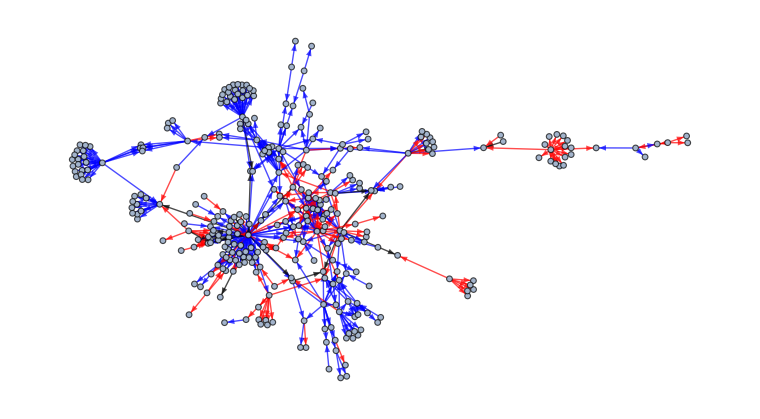

```mathematica
SimpleGraph@Subgraph[gEC,WeaklyConnectedComponents[SimpleGraph@gEC][[1]]]
```

```mathematica
{VertexCount[#],EdgeCount[#]}&@gEC
```

{423,578}

Import the 100 randomized networks:

```mathematica
SetDirectory["/Ecoli random networks"]
```

```mathematica
gRandsEC=Import[#,"Data"]&/@FileNames[];
```

```mathematica
gRandsEC//Dimensions
```

{100,519,3}

Detecting network motifs using mathematica:

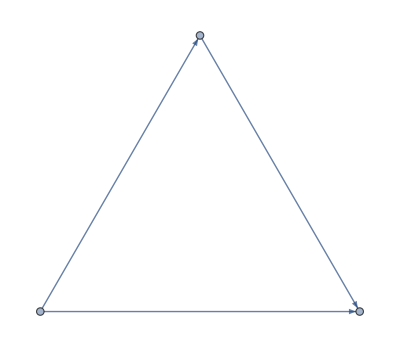
{{{-Graphics-,59}},{},{{-Graphics-,42,11.4267}}}

```mathematica
NetMotFinderAllUp3[gEC,1]
```

Detecting network motifs using mFinder:

```mathematica
coliNetMFinder3N=Import["/coliNet3N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[coliNetMFinder3N[[36;;38]]]]]
```

-Graphics-

```mathematica
coliNetMFinder4N=Import["/coliNet4N_OUT.txt","Data"];
```

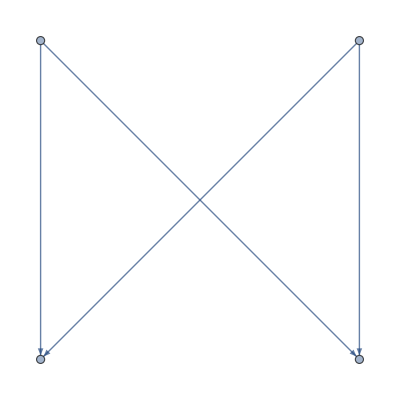
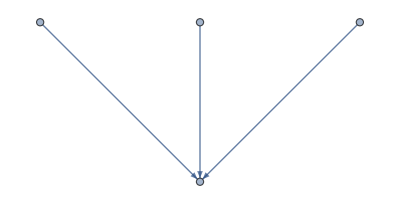

```mathematica
{AdjacencyGraph[ToExpression[StringSplit[coliNetMFinder4N[[36;;39]]]]],AdjacencyGraph[ToExpression[StringSplit[coliNetMFinder4N[[43;;46]]]]]}
```

```mathematica
motCombsEC2=EnrichedCombsMFinderRandUpTo3[gEC,Graph[DirectedEdge@@@#[[;;,;;2]]]&/@gRandsEC,{-Graphics-,-Graphics-},{1,7}]//Quiet;
```

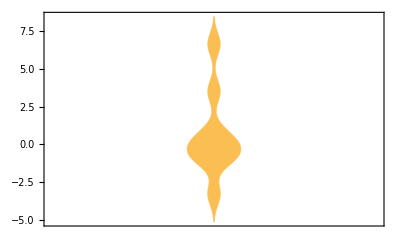

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombsEC2[[1]]),PlotRange->All]//Quiet
```

```mathematica
{Select[motCombsEC2[[2]],#[[2]]>0&][[;;,1]],Select[motCombsEC2[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-},{}}

```mathematica
NormalPValue[6.624054857062341]
```

OneSidedPValue→1.74738×10^-11

```mathematica
motCombsEC2[[2;;]]
```

{{{-Graphics-,6.62405,0.005}},, | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  | -Graphics- | -Graphics-
-Graphics- |  |  |  | -Graphics-}

Analysis with randomize networks that also keep a more accurate distribution of self loops in the network:

```mathematica
SetDirectory["/Ecoli random networks with self loops"]
```

```mathematica
gRandMFsAR=Import[#,"Data"]&/@FileNames[];
```

```mathematica
gRandMFsAR2=Table[Graph[DirectedEdge@@@Union[Join[Complement[gRandMFsAR[[i,;;,;;2]],Select[gRandMFsAR[[i,;;,;;2]],#[[2]]>Max[VertexList[gEC]]&]],{#,#}&/@Union[Select[gRandMFsAR[[i,;;,;;2]],#[[2]]>Max[VertexList[gEC]]&][[;;,1]]]]]],{i,1,Length@gRandMFsAR}];
```

```mathematica
gRandMFsAR3=Table[Graph[DirectedEdge@@@Join[EdgeList[gRandMFsAR2[[i]]],{#,#}&/@RandomSample[Union[Complement[VertexList[gRandMFsAR2[[i]]],Select[EdgeList[gRandMFsAR2[[i]]],#[[1]]==#[[2]]&][[;;,1]]]],Length[EdgeList[gEC]]-Length[EdgeList[gRandMFsAR2[[i]]]]]]],{i,1,Length@gRandMFsAR2}];
```

```mathematica
motCombsEC3=EnrichedCombsMFinderRand2UpTo3[gEC,gRandMFsAR3,{-Graphics-,-Graphics-},{1,7}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombsEC3[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
{Select[motCombsEC3[[2]],#[[2]]>0&][[;;,1]],Select[motCombsEC3[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-},{}}

```mathematica
NormalPValue[2.855339260491044]
```

OneSidedPValue→0.00214954

```mathematica
motCombsEC3[[2;;]]
```

{{{-Graphics-,2.85534,0.01}},, | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  | -Graphics- | -Graphics-
-Graphics- |  |  |  | -Graphics-}

```mathematica
motCombs2ShEC=EnrichedCombs2ShMFinderRandUpTo3[SimpleGraph@gEC,SimpleGraph[DirectedEdge@@@#[[;;,;;2]]]&/@gRandsEC,{-Graphics-},{7}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShEC[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
{Select[motCombs2ShEC[[2]],#[[2]]>0&][[;;,1]],Select[motCombs2ShEC[[2]],#[[2]]<0&][[;;,1]]}
```

{{},{}}

```mathematica
motCombs2ShEC[[3;;]]
```

{, | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  | -Graphics- | -Graphics-
-Graphics- |  |  | -Graphics-}

## C. elegans neural network:

Import the network:

```mathematica
CEData=Import["/neuralCElegans_net.dat"];
```

```mathematica
gCE=Graph[(DirectedEdge@@@Union[CEData[[;;,;;2]]]),DirectedEdges->True,GraphLayout->"RadialEmbedding"];
```

```mathematica
{VertexCount[#],EdgeCount[#]}&@gCE
```

{297,2345}

Import the 100 randomized networks:

```mathematica
SetDirectory["/CE random networks"]
```

```mathematica
gRandsCE=Import[#,"Data"]&/@FileNames[];
```

```mathematica
gRandsCE//Dimensions
```

{100,2345,3}

Detecting network motifs using mathematica:

```mathematica
NetMotFinderAllUp3[gCE,1]
```

{{},{{-Graphics-,197,21.042}},{{-Graphics-,542,33.2116},{-Graphics-,312,20.0549},{-Graphics-,148,15.7897},{-Graphics-,16,12.5037},{-Graphics-,315,9.90744},{-Graphics-,2828,8.6809},{-Graphics-,2595,5.51953},{-Graphics-,179,4.95175}}}

Detecting network motifs using mFinder:

```mathematica
CEMFinder3N=Import["/CENet3N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[CEMFinder3N[[#]]]],DirectedEdges->True]&/@{36;;38,42;;44,48;;50,54;;56,60;;62,66;;68}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
CEMFinder4N=Import["/CENet4N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[CEMFinder4N[[#]]]],DirectedEdges->True]&/@{36;;39,43;;46,50;;53,57;;60,64;;67,71;;74,78;;81}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
motCombsCE2=EnrichedCombsMFinderRandUpTo3[gCE,Graph[DirectedEdge@@@#[[;;,;;2]]]&/@gRandsCE,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{7,8,12,13,14,15}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombsCE2[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
{SortBy[Select[motCombsCE2[[2]],#[[2]]>0&],-#[[2]]&][[;;,1]],SortBy[Select[motCombsCE2[[2]],#[[2]]<0&],#[[2]]&][[;;,1]]}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
SortBy[Select[motCombsCE2[[2]],#[[2]]>0&],-#[[2]]&][[;;,2]]
```

{8.57175,8.08524,7.79096,7.46719,5.24619,4.11625,3.79227,3.00201,2.97872}

```mathematica
NormalPValue[#][[2]]&/@SortBy[Select[motCombsCE2[[2]],#[[2]]>0&],-#[[2]]&][[;;,2]]
```

{5.09615×10^-18,3.10202×10^-16,3.3251×10^-15,4.09613×10^-14,7.76385×10^-8,0.000019254,0.0000746385,0.00134101,0.00144727}

```mathematica
SortBy[Select[motCombsCE2[[2]],#[[2]]>0&],-#[[2]]&][[;;,3]]
```

{0.00047619,0.000952381,0.00142857,0.00190476,0.00238095,0.00333333,0.00380952,0.00428571,0.0047619}

```mathematica
motCombs2ShCE=EnrichedCombs2ShMFinderRandUpTo3[gCE,Graph[DirectedEdge@@@#[[;;,;;2]]]&/@gRandsCE,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{7,8,12,13,14,15}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShCE[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
Select[motCombs2ShCE[[2]],#[[2]]<0&][[;;,1]]//Length
```

34

```mathematica
Select[motCombs2ShCE[[2]],#[[2]]>0&][[;;,2;;]]
```

{{3.05791,0.0192982},{2.18928,0.0263158}}

```mathematica
NormalPValue/@Select[motCombs2ShCE[[2]],#[[2]]>0&][[;;,2]]
```

{OneSidedPValue→0.00111443,OneSidedPValue→0.0142883}

```mathematica
{Select[motCombs2ShCE[[2]],#[[2]]>0&][[;;,1]],Select[motCombs2ShCE[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

Exploring the frequencies of the core topologies and their extensions (Figure S3):

```mathematica
circuitComp[-Graphics-,-Graphics-][[;;6]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
totFFLFFL1CE=NumSubG[gCE,#]&/@circuitComp[-Graphics-,-Graphics-][[;;6]];
```

```mathematica
totFFLFFL1CE
```

{2710,6088,8468,3629,9891,57430}

```mathematica
totFFLFFL2CE=NumSubG[gCE,#]&/@circuitComp[-Graphics-,-Graphics-][[7;;]];
```

```mathematica
totFFLFFL2CE
```

{1001,2436,2110,1503,929,1343}

```mathematica
totFFLFFL1CERand=NumSubG[Graph[DirectedEdge@@@gRandsCE[[1,;;,;;2]]],#]&/@circuitComp[-Graphics-,-Graphics-][[;;6]];
```

```mathematica
totFFLFFL1CERand
```

{6966,7212,9286,2068,4292,114334}

```mathematica
totFFLFFL2CERand=NumSubG[Graph[DirectedEdge@@@gRandsCE[[1,;;,;;2]]],#]&/@circuitComp[-Graphics-,-Graphics-][[7;;]];
```

```mathematica
totFFLFFL2CERand
```

{1170,4440,1591,5134,1171,2391}

```mathematica
CEC1=ExtComb[-Graphics-,-Graphics-,-Graphics-];
```

```mathematica
CEC2=ExtComb[-Graphics-,-Graphics-,-Graphics-];
```

```mathematica
CEC3=ExtComb[-Graphics-,-Graphics-,-Graphics-];
```

```mathematica
CEC4=ExtComb[-Graphics-,-Graphics-,-Graphics-];
```

```mathematica
CEC5=ExtComb[#,-Graphics-,-Graphics-]&/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
CEC1F=NumSubG[gCE,#]&/@CEC1;//Quiet
```

Sort::normal: Nonatomic expression expected at position 1 in Sort[1].

Sort::normal: Nonatomic expression expected at position 1 in Sort[2].

Sort::normal: Nonatomic expression expected at position 1 in Sort[3].

General::stop: Further output of Sort::normal will be suppressed during this calculation.

```mathematica
SortBy[Select[{CEC1F,CEC1}ᵀ,#[[1]]>0&],-#[[1]]&][[1]]
```

{3222,-Graphics-}

```mathematica
BarChart[#[[1]]]&@(SortBy[Select[{CEC1F,CEC1}ᵀ,#[[1]]>0&],-#[[1]]&]ᵀ)
```

-Graphics-

```mathematica
CEC2F=NumSubG[gCE,#]&/@CEC2;//Quiet
```

```mathematica
SortBy[Select[{CEC2F,CEC2}ᵀ,#[[1]]>0&],-#[[1]]&][[1]]
```

{2426,-Graphics-}

```mathematica
BarChart[#[[1]]]&@(SortBy[Select[{CEC2F,CEC2}ᵀ,#[[1]]>0&],-#[[1]]&]ᵀ)
```

-Graphics-

```mathematica
CEC3F=NumSubG[gCE,#]&/@CEC3;//Quiet
```

```mathematica
SortBy[Select[{CEC3F,CEC3}ᵀ,#[[1]]>0&],-#[[1]]&][[1]]
```

{5258,-Graphics-}

```mathematica
BarChart[#[[1]]]&@(SortBy[Select[{CEC3F,CEC3}ᵀ,#[[1]]>0&],-#[[1]]&]ᵀ)
```

-Graphics-

```mathematica
CEC4F=NumSubG[gCE,#]&/@CEC4;//Quiet
```

```mathematica
SortBy[Select[{CEC4F,CEC4}ᵀ,#[[1]]>0&],-#[[1]]&][[1]]
```

{935,-Graphics-}

```mathematica
BarChart[#[[1]]]&@(SortBy[Select[{CEC4F,CEC4}ᵀ,#[[1]]>0&],-#[[1]]&]ᵀ)
```

-Graphics-

```mathematica
CEC5F=Map[NumSubG[gCE,#]&,CEC5,{2}];//Quiet
```

```mathematica
Table[SortBy[Select[{CEC5F[[i]],CEC5[[i]]}ᵀ,#[[1]]>0&],-#[[1]]&][[1]],{i,1,5}]
```

{{8468,-Graphics-},{9891,-Graphics-},{2710,-Graphics-},{6088,-Graphics-},{3629,-Graphics-}}

```mathematica
BarChart[#[[1]]]&/@Table[SortBy[Select[{CEC5F[[i]],CEC5[[i]]}ᵀ,#[[1]]>0&],-#[[1]]&]ᵀ,{i,1,5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-}
```

```mathematica
CEC6=ExtComb[-Graphics-,-Graphics-,-Graphics-];
```

```mathematica
CEC6F=Map[NumSubG[gCE,#]&,CEC6,{1}];//Quiet
```

```mathematica
SortBy[Select[{CEC6F,CEC6}ᵀ,#[[1]]>0&],-#[[1]]&]
```

{{2110,-Graphics-},{491,-Graphics-},{20,-Graphics-},{16,-Graphics-}}

```mathematica
BarChart[#[[1]]]&@(SortBy[Select[{CEC6F,CEC6}ᵀ,#[[1]]>0&],-#[[1]]&]ᵀ)
```

-Graphics-

```mathematica
CEC7=ExtComb[-Graphics-,-Graphics-,-Graphics-];
```

```mathematica
CEC7
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
CEC7F=Map[NumSubG[gCE,#]&,CEC7,{1}];//Quiet
```

```mathematica
SortBy[Select[{CEC7F,CEC7}ᵀ,#[[1]]>0&],-#[[1]]&]
```

{{28,-Graphics-},{15,-Graphics-},{4,-Graphics-}}

```mathematica
BarChart[#[[1]]]&@(SortBy[Select[{CEC7F,CEC7}ᵀ,#[[1]]>0&],-#[[1]]&]ᵀ)
```

-Graphics-

## Electronic circuits:

Import the networks:

```mathematica
elecNet1Data=Import["/s208_st_UriWeb.txt","Data"];
```

```mathematica
elecNet2Data=Import["/s420_st_UriWeb.txt","Data"];
```

```mathematica
elecNet3Data=Import["/s838_st_UriWeb.txt","Data"];
```

```mathematica
gE1=Graph[Union[DirectedEdge@@@elecNet1Data[[;;,;;2]]],DirectedEdges->True];
```

```mathematica
gE2=Graph[Union[DirectedEdge@@@elecNet2Data[[;;,;;2]]],DirectedEdges->True];
```

```mathematica
gE3=Graph[Union[DirectedEdge@@@elecNet3Data[[;;,;;2]]],DirectedEdges->True];
```

```mathematica
{VertexCount[#],EdgeCount[#]}&/@{gE1,gE2,gE3}
```

{{122,189},{252,399},{512,819}}

Detecting network motifs with mathematica:

```mathematica
NetMotFinderAllUp3[gE1,1]
```

{{},{},{{-Graphics-,10,9.69223}}}

```mathematica
NetMotFinderAllUp3[gE2,1]
```

{{},{},{{-Graphics-,20,17.2739}}}

```mathematica
NetMotFinderAllUp3[gE3,1]
```

{{},{},{{-Graphics-,40,38.8572}}}

Detecting network motifs with mFinder:

```mathematica
E1MFinder3N=Import["/Elec1Net3N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[E1MFinder3N[[#]]]],DirectedEdges->True]&/@{36;;38}
```

{-Graphics-}

```mathematica
E2MFinder3N=Import["/Elec2Net3N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[E2MFinder3N[[#]]]],DirectedEdges->True]&/@{36;;38}
```

{-Graphics-}

```mathematica
E3MFinder3N=Import["/Elec3Net3N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[E3MFinder3N[[#]]]],DirectedEdges->True]&/@{36;;38}
```

{-Graphics-}

```mathematica
E3MFinder4N=Import["/Elec3Net4N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[E3MFinder4N[[#]]]],DirectedEdges->True]&/@{36;;39,43;;46,50;;53}
```

{-Graphics-,-Graphics-,-Graphics-}

Import the 100 randomized networks:

```mathematica
SetDirectory["/s208 random networks"]
```

```mathematica
gRandsE1=Import[#,"Data"]&/@FileNames[];
```

```mathematica
gRandsE1//Dimensions
```

{100,189,3}

```mathematica
motCombs2ShE1=EnrichedCombs2ShMFinderRandUpTo3[gE1,Graph[DirectedEdge@@@#[[;;,;;2]]]&/@gRandsE1,{-Graphics-},{11}]//Quiet;
```

```mathematica
((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShE1[[1]])
```

{1.66768}

```mathematica
NormalPValue[1.667679879476386]
```

OneSidedPValue→0.0476896

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShE1[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
{Select[motCombs2ShE1[[2]],#[[2]]>0&][[;;,1]],Select[motCombs2ShE1[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-},{}}

```mathematica
SetDirectory["/s420 random networks"]
```

```mathematica
gRandsE2=Import[#,"Data"]&/@FileNames[];
```

```mathematica
motCombs2ShE2=EnrichedCombs2ShMFinderRandUpTo3[gE2,Graph[DirectedEdge@@@#[[;;,;;2]]]&/@gRandsE2,{-Graphics-},{11}]//Quiet;
```

```mathematica
((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShE2[[1]])
```

{2.27704}

```mathematica
NormalPValue[2.277038293035184]
```

OneSidedPValue→0.011392

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShE2[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
{Select[motCombs2ShE2[[2]],#[[2]]>0&][[;;,1]],Select[motCombs2ShE2[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-},{}}

```mathematica
SetDirectory["/s838 random networks"]
```

```mathematica
gRandsE3=Import[#,"Data"]&/@FileNames[];
```

```mathematica
motCombs2ShE3=EnrichedCombs2ShMFinderRandUpTo3[gE3,Graph[DirectedEdge@@@#[[;;,;;2]]]&/@gRandsE3,{-Graphics-},{11}]//Quiet;
```

```mathematica
((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShE3[[1]])
```

{3.12422}

```mathematica
NormalPValue[3.124218437029894]
```

OneSidedPValue→0.00089139

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShE3[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
{Select[motCombs2ShE3[[2]],#[[2]]>0&][[;;,1]],Select[motCombs2ShE3[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-},{}}

```mathematica
ECC1=ExtComb[-Graphics-,-Graphics-,-Graphics-];
```

```mathematica
ECC1
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ECC1F=Map[NumSubG[gE1,#]&,ECC1,{1}];//Quiet
```

```mathematica
ECC1F
```

{2,0,0}

```mathematica
SortBy[Select[{ECC1F,ECC1}ᵀ,#[[1]]>0&],-#[[1]]&]
```

{{2,-Graphics-}}

```mathematica
ECC2F=Map[NumSubG[gE2,#]&,ECC1,{1}];//Quiet
```

```mathematica
ECC2F
```

{4,0,0}

```mathematica
SortBy[Select[{ECC2F,ECC1}ᵀ,#[[1]]>0&],-#[[1]]&]
```

{{4,-Graphics-}}

```mathematica
ECC3F=Map[NumSubG[gE3,#]&,ECC1,{1}];//Quiet
```

```mathematica
ECC3F
```

{8,0,0}

```mathematica
SortBy[Select[{ECC3F,ECC1}ᵀ,#[[1]]>0&],-#[[1]]&]
```

{{8,-Graphics-}}

## Food Webs:

Import the network:

```mathematica
foodWebData=Import["/FW-StMartin_net.dat"];
```

```mathematica
gFW=Graph[Union[DirectedEdge@@@foodWebData[[;;,;;2]]],DirectedEdges->True,GraphLayout->"BalloonEmbedding"];
```

```mathematica
{VertexCount[#],EdgeCount[#]}&@gFW
```

{45,224}

Detecting network motifs with mathematica:

```mathematica
NetMotFinderOnlyUp3[gFW,1]
```

{{},{},{{-Graphics-,280,4.52184},{-Graphics-,592,4.3239}}}

Detecting network motifs with mFinder:

```mathematica
FWMFinder3N=Import["/FWSM3Net3N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[FWMFinder3N[[#]]]],DirectedEdges->True]&/@{36;;38}
```

ToExpression::sntxi: Incomplete expression; more input is needed .

AdjacencyGraph::matsq: Argument {{},{Full,list,of,subgraphs,size,3,$Failed},{}} at position 2 is not a non-empty square matrix.

{AdjacencyGraph[Automatic,{{},{Full,list,of,subgraphs,size,3,$Failed},{}},DirectedEdges→True]}

```mathematica
FWMFinder4N=Import["/FWSM3Net4N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[FWMFinder4N[[#]]]],DirectedEdges->True]&/@{36;;39,43;;46,50;;53,57;;60,64;;67,71;;74,78;;81,85;;88}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Import the 100 randomized networks:

```mathematica
SetDirectory["/St Martin random network"]
```

```mathematica
gRandsFW=Import[#,"Data"]&/@FileNames[];
```

```mathematica
gRandsFW//Dimensions
```

{100,224,3}

```mathematica
motCombsFW2=EnrichedCombsMFinderRandUpTo3[gFW,Graph[DirectedEdge@@@#[[;;,;;2]]]&/@gRandsFW,{-Graphics-,-Graphics-},{4,7}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombsFW2[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
SortBy[Select[motCombsFW2[[2]],#[[2]]>0&],-#[[2]]&][[;;,3]]
```

{0.0190476}

```mathematica
{SortBy[Select[motCombsFW2[[2]],#[[2]]>0&],-#[[2]]&][[;;,1]],SortBy[Select[motCombsFW2[[2]],#[[2]]<0&],#[[2]]&][[;;,1]]}
```

{{-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
motCombs2ShFW=EnrichedCombs2ShMFinderRandUpTo3[gFW,Graph[DirectedEdge@@@#[[;;,;;2]]]&/@gRandsFW,{-Graphics-,-Graphics-},{4,7}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShFW[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
NormalPValue/@Select[motCombs2ShFW[[2]],#[[2]]>0&][[;;,2]]
```

{OneSidedPValue→1.87395×10^-7,OneSidedPValue→0.0129006}

```mathematica
{Select[motCombs2ShFW[[2]],#[[2]]>0&][[;;,1]],Select[motCombs2ShFW[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

Analysis of frequencies of core topologies and their extensions (Figure S3):

```mathematica
FWC1=ExtComb[-Graphics-,-Graphics-,-Graphics-];
```

```mathematica
FWC1F=NumSubG[gFW,#]&/@FWC1;//Quiet
```

```mathematica
(SortBy[Select[{FWC1F,FWC1}ᵀ,#[[1]]>0&],-#[[1]]&])[[1]]
```

{2052,-Graphics-}

```mathematica
BarChart[#[[1]]]&@(SortBy[Select[{FWC1F,FWC1}ᵀ,#[[1]]>0&],-#[[1]]&]ᵀ)
```

-Graphics-

```mathematica
{-Graphics-,-Graphics-}
```

```mathematica
FWC2=ExtComb[-Graphics-,-Graphics-,-Graphics-];
```

```mathematica
FWC2
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
FWC2F=NumSubG[gFW,#]&/@FWC2;//Quiet
```

```mathematica
(SortBy[Select[{FWC2F,FWC2}ᵀ,#[[1]]>0&],-#[[1]]&])
```

{{457,-Graphics-},{263,-Graphics-}}

```mathematica
BarChart[#[[1]]]&@((SortBy[Select[{FWC2F,FWC2}ᵀ,#[[1]]>0&],-#[[1]]&])ᵀ)
```

-Graphics-

```mathematica
FWC3=ExtComb[-Graphics-,-Graphics-,-Graphics-];
```

```mathematica
FWC3
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
FWC3F=NumSubG[gFW,#]&/@FWC3;//Quiet
```

```mathematica
(SortBy[Select[{FWC3F,FWC3}ᵀ,#[[1]]>0&],-#[[1]]&])
```

{{203,-Graphics-},{157,-Graphics-}}

```mathematica
BarChart[#[[1]]]&@(SortBy[Select[{FWC3F,FWC3}ᵀ,#[[1]]>0&],-#[[1]]&]ᵀ)
```

-Graphics-

## Citation network:

Import the network:

```mathematica
citData=Import["/centrality_literature.paj"];
```

```mathematica
citData2=Partition[StringSplit[StringSplit[StringSplit[citData,"*Arcs"][[2]],"*Edges"][[1]]],{3}];
```

```mathematica
citData2//Dimensions
```

{613,3}

```mathematica
gCit=Graph[DirectedEdge@@{#[[1]],#[[2]]}&/@citData2,DirectedEdges->True,GraphLayout->"BalloonEmbedding"];
```

```mathematica
{VertexCount[#],EdgeCount[#]}&@gCit
```

{118,613}

Detecting network motifs with mathematica:

```mathematica
NetMotFinderOnlyUp3[gCit,1]
```

{{},{},{{-Graphics-,1107,6.31086}}}

Detecting network motifs with mFinder:

```mathematica
CitMFinder3N=Import["/CitNet3N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[CitMFinder3N[[#]]]],DirectedEdges->True]&/@{36;;38}
```

{-Graphics-}

```mathematica
CitMFinder4N=Import["/CitNet4N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[CitMFinder4N[[#]]]],DirectedEdges->True]&/@{36;;39,43;;46,50;;53,57;;60,64;;67,71;;74,78;;81,85;;88}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Import 100 randomized networks:

```mathematica
SetDirectory["/centrality_citations_random networks"]
```

```mathematica
gRandsCit=Import[#,"Data"]&/@FileNames[];
```

```mathematica
gRandsCit//Dimensions
```

{100,613,3}

```mathematica
motCombsCit2=EnrichedCombsMFinderRandUpTo3[gCit,Graph[DirectedEdge@@@#[[;;,;;2]]]&/@gRandsCit,{-Graphics-},{7}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombsCit2[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
NormalPValue/@SortBy[Select[motCombsCit2[[2]],#[[2]]>0&],-#[[2]]&][[;;,2]]
```

{OneSidedPValue→0.000195357,OneSidedPValue→0.00829955}

```mathematica
SortBy[Select[motCombsCit2[[2]],#[[2]]>0&],-#[[2]]&][[;;,3]]
```

{0.00833333,0.0166667}

```mathematica
{SortBy[Select[motCombsCit2[[2]],#[[2]]>0&],-#[[2]]&][[;;,1]],SortBy[Select[motCombsCit2[[2]],#[[2]]<0&],#[[2]]&][[;;,1]]}
```

{{-Graphics-,-Graphics-},{}}

```mathematica
motCombs2ShCit=EnrichedCombs2ShMFinderRandUpTo3[gCit,Graph[DirectedEdge@@@#[[;;,;;2]]]&/@gRandsCit,{-Graphics-},{7}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShCit[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
{Select[motCombs2ShCit[[2]],#[[2]]>0&][[;;,1]],Select[motCombs2ShCit[[2]],#[[2]]<0&][[;;,1]]}
```

{{},{-Graphics-}}

Analysis of frequencies of core topologies and their extensions:

```mathematica
{-Graphics-,-Graphics-}
```

```mathematica
CitC1=ExtComb[-Graphics-,-Graphics-,-Graphics-];
```

```mathematica
CitC1//Length
```

222

```mathematica
CitC1F=NumSubG[gCit,#]&/@CitC1;//Quiet
```

```mathematica
(SortBy[Select[{CitC1F,CitC1}ᵀ,#[[1]]>0&],-#[[1]]&])[[;;5]]
```

{{8159,-Graphics-},{3512,-Graphics-},{3405,-Graphics-},{2774,-Graphics-},{1516,-Graphics-}}

```mathematica
BarChart[#[[1]]]&@(SortBy[Select[{CitC1F,CitC1}ᵀ,#[[1]]>0&],-#[[1]]&]ᵀ)
```

-Graphics-

```mathematica
CitC2=ExtComb[-Graphics-,-Graphics-,-Graphics-];
```

```mathematica
CitC2//Length
```

234

```mathematica
CitC2F=NumSubG[gCit,#]&/@CitC2;//Quiet
```

```mathematica
(SortBy[Select[{CitC2F,CitC2}ᵀ,#[[1]]>0&],-#[[1]]&])[[;;5]]
```

{{810,-Graphics-},{331,-Graphics-},{310,-Graphics-},{275,-Graphics-},{192,-Graphics-}}

```mathematica
BarChart[#[[1]]]&@((SortBy[Select[{CitC2F,CitC2}ᵀ,#[[1]]>0&],-#[[1]]&])ᵀ)
```

-Graphics-

## Social network:

Import the network:

```mathematica
FrData=Import["/Friendship-network_data_2013.csv"];
```

```mathematica
FrData2=(StringSplit[#," "]&/@FrData)[[;;,1]];
```

```mathematica
gFr=Graph[DirectedEdge@@@FrData2,DirectedEdges->True,GraphLayout->"RadialEmbedding"];
```

```mathematica
{VertexCount[#],EdgeCount[#]}&@gFr
```

{134,668}

Detecting network motifs with mathematica:

```mathematica
NetMotFinderAllUp3[gFr,1]
```

{{},{{-Graphics-,262,62.6209}},{{-Graphics-,200,1999.9},{-Graphics-,137,93.2153},{-Graphics-,416,86.3426},{-Graphics-,50,14.919},{-Graphics-,40,13.812},{-Graphics-,402,4.09257},{-Graphics-,364,3.33902}}}

Detecting network motifs with mFinder:

```mathematica
FrMFinder3N=Import["/FriendNet3N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[FrMFinder3N[[#]]]],DirectedEdges->True]&/@{36;;38,42;;44,48;;50,54;;56,60;;62}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FrMFinder3N//TableForm
```

Summary motif results
   =====================
mfinder Version 1.20

MOTIF FINDER RESULTS:

	Network name: FriendshipMFinder.txt
	Network type: Directed
	Num of Nodes: 1828 Num of Edges: 668
	Num of Nodes with edges: 134
	Maximal out degree (out-hub) : 16
	Maximal in degree (in-hub) : 15
	Roots num: 3 Leaves num: 1
	Single Edges num: 144 Mutual Edges num: 262

	Motif size searched  3
	Total number of 3-node subgraphs : 1944
	Number of random networks generated : 100
	Random networks generation method: Switches (with metropolis)

The following motifs were found:

Criteria taken : Nreal Zscore > 2.00
                 Pval ignored (due to small number of random networks)
                 Mfactor > 1.10
                 Uniqueness >= 4



	Full list includes 5 motifs
MOTIF	NREAL	NRAND		NREAL	NREAL	UNIQ	CREAL
ID		STATS		ZSCORE	PVAL	VAL	[MILI]	

38	15	4.9+-2.1	4.90	0.000	5	7.72

0 1 1 
0 0 1 
0 0 0 

46	50	5.5+-2.4	18.17	0.000	8	25.72

0 1 1 
1 0 1 
0 0 0 

108	40	5.6+-2.2	15.31	0.000	13	20.58

0 0 1 
1 0 1 
1 0 0 

110	137	22.9+-5.0	22.98	0.000	18	70.47

0 1 1 
1 0 1 
1 0 0 

238	200	14.1+-3.5	52.42	0.000	28	102.88

0 1 1 
1 0 1 
1 1 0 




Full list of subgraphs size 3 ids:

	( Total num of different subgraphs size 3 is : 13 )

MOTIF	NREAL	NRAND		NREAL	NREAL	CREAL	UNIQ
ID		STATS		ZSCORE	PVAL	[MILI]	
6	110	154.5+-2.9	-15.12	1.000	56.58	14

12	124	137.0+-3.3	-3.99	1.000	63.79	14

14	402	608.7+-7.3	-28.46	1.000	206.79	22

36	77	131.6+-2.9	-19.02	1.000	39.61	15

38	15	4.9+-2.1	4.90	0.000	7.72	5

46	50	5.5+-2.4	18.17	0.000	25.72	8

74	364	550.6+-7.2	-26.06	1.000	187.24	22

78	416	1087.8+-11.6	-57.97	1.000	213.99	23

98	0	0.3+-0.5	-0.53	1.000	0.00	0

102	9	5.3+-2.3	1.60	0.100	4.63	5

108	40	5.6+-2.2	15.31	0.000	20.58	13

110	137	22.9+-5.0	22.98	0.000	70.47	18

238	200	14.1+-3.5	52.42	0.000	102.88	28



 (Application total runtime was:    9.0 seconds.)

 (Real network processing runtime was:    0.0 seconds.)

 (Single Random network processing runtime was:    0.1 seconds.)

```mathematica
FrMFinder4N=Import["/FriendshipMFinder_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[FrMFinder4N[[#]]]],DirectedEdges->True]&/@{36;;39,43;;46,50;;53,57;;60,64;;67,71;;74,78;;81}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Import 100 randomized networks:

```mathematica
SetDirectory["/Friendship_random networks"]
```

```mathematica
gRandsFr=Import[#,"Data"]&/@FileNames[];
```

```mathematica
gRandsFr//Dimensions
```

{100,668,3}

```mathematica
motCombs2ShFr=EnrichedCombs2ShMFinderRandUpTo3[gFr,Graph[DirectedEdge@@@#[[;;,;;2]]]&/@gRandsFr,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{7,8,10,13,14,15}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShFr[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
SortBy[Select[motCombs2ShFr[[2]]/.ComplexInfinity->0,#[[2]]>0&],-#[[2]]&][[;;,3]]
```

{0.001,0.002}

```mathematica
NormalPValue/@SortBy[Select[motCombs2ShFr[[2]]/.ComplexInfinity->0,#[[2]]>0&],-#[[2]]&][[;;,2]]
```

{OneSidedPValue→0.000019333,OneSidedPValue→0.000118922}

```mathematica
{SortBy[Select[motCombs2ShFr[[2]]/.ComplexInfinity->0,#[[2]]>0&],-#[[2]]&][[;;,1]],SortBy[Select[motCombs2ShFr[[2]]/.ComplexInfinity->0,#[[2]]<0&],#[[2]]&][[;;,1]]}
```

{{-Graphics-,-Graphics-},{}}

Analysis of frequencies of core topologies and their extensions:

```mathematica
SocFr1=ExtComb[-Graphics-,-Graphics-,-Graphics-];
```

```mathematica
SocFr1
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
SocFr1F=NumSubG[gFr,#]&/@SocFr1;//Quiet
```

```mathematica
(SortBy[Select[{SocFr1F,SocFr1}ᵀ,#[[1]]>0&],-#[[1]]&])
```

{{5,-Graphics-},{2,-Graphics-}}

```mathematica
BarChart[#[[1]]]&@((SortBy[Select[{SocFr1F,SocFr1}ᵀ,#[[1]]>0&],-#[[1]]&])ᵀ)
```

-Graphics-

```mathematica
SocFr2=ExtComb[-Graphics-,-Graphics-,-Graphics-];
```

```mathematica
SocFr2
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
SocFr2F=NumSubG[gFr,#]&/@SocFr2;//Quiet
```

```mathematica
(SortBy[Select[{SocFr2F,SocFr2}ᵀ,#[[1]]>0&],-#[[1]]&])
```

{{13,-Graphics-},{10,-Graphics-},{6,-Graphics-}}

```mathematica
BarChart[#[[1]]]&@((SortBy[Select[{SocFr2F,SocFr2}ᵀ,#[[1]]>0&],-#[[1]]&])ᵀ)
```

-Graphics-

## Word Adjacency network (English):

Import the network:

```mathematica
LangNetEngData=Import["/darwinbookinter_st_UriWeb.txt","Data"];
```

```mathematica
gEng=Graph[Union[DirectedEdge@@@LangNetEngData[[;;,;;2]]],DirectedEdges->True]
```

Downsampling the network:

```mathematica
sampGraph[g_,sz_]:=Module[{s0,s},
s0=RandomChoice[VertexList[g]];
s=ConstantArray[0,sz];
s[[1]]=s0;
s[[2]]=RandomChoice[DeleteCases[VertexList[NeighborhoodGraph[g,s0]],s0]];
Table[s[[i]]=If[RandomReal[{0,1}]<.85,RandomChoice[DeleteCases[VertexList[NeighborhoodGraph[g,s[[i-1]]]],s[[i-1]]]],RandomChoice[DeleteCases[VertexList[NeighborhoodGraph[g,s0]],s0]]],{i,3,Round[sz/3]}];
s0=If[Length[Union[s[[;;Round[sz/3]]]]]<Round[1/2 sz/3],RandomChoice[VertexList[g]],s0];
Table[s[[i]]=If[RandomReal[{0,1}]<.85,RandomChoice[DeleteCases[VertexList[NeighborhoodGraph[g,s[[i-1]]]],s[[i-1]]]],RandomChoice[DeleteCases[VertexList[NeighborhoodGraph[g,s0]],s0]]],{i,Round[sz/3]+1,Round[2 sz/3]}];
s0=If[Length[Union[s[[;;Round[2 sz/3]]]]]<Round[1/2 2 sz/3],RandomChoice[VertexList[g]],s0];
Table[s[[i]]=If[RandomReal[{0,1}]<.85,RandomChoice[DeleteCases[VertexList[NeighborhoodGraph[g,s[[i-1]]]],s[[i-1]]]],RandomChoice[DeleteCases[VertexList[NeighborhoodGraph[g,s0]],s0]]],{i,Round[2 sz/3]+1,sz}];
Subgraph[g,s]
]
```

```mathematica
gJapDS=sampGraph[gJap,2000];
```

Import the downsampled network:

```mathematica
EngDS=Import["/EngDSMfinder.txt","Data"];
```

```mathematica
gEngDS=Graph[DirectedEdge@@@EngDS[[;;,;;2]],DirectedEdges->True,GraphLayout->"RadialEmbedding"];
```

```mathematica
gEngDS
```

-Graphics-

```mathematica
{VertexCount[#],EdgeCount[#]}&@gEngDS
```

{315,4055}

Detecting network motifs with mathematica:

```mathematica
NetMotFinderAllUp3[gEngDS,1]
```

{{},{},{{-Graphics-,9280,13.1608},{-Graphics-,36232,11.859},{-Graphics-,54260,11.1435},{-Graphics-,2266,10.1068},{-Graphics-,26172,9.07145}}}

Detecting network motifs with mFinder:

```mathematica
EngDSMFinder3N=Import["/EngDSNet3N_OUT.txt","Data"];
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
EngDSMFinder4N=Import["/EngDSMfinder_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[EngDSMFinder4N[[#]]]],DirectedEdges->True]&/@{36;;39,43;;46,50;;53,57;;60,64;;67,71;;74,78;;81}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
EngDSMFinder4N//TableForm
```

Summary motif results
   =====================
mfinder Version 1.20

MOTIF FINDER RESULTS:

	Network name: EngDSMfinder.txt
	Network type: Directed
	Num of Nodes: 7683 Num of Edges: 4055
	Num of Nodes with edges: 315
	Maximal out degree (out-hub) : 155
	Maximal in degree (in-hub) : 131
	Roots num: 7 Leaves num: 14
	Single Edges num: 3131 Mutual Edges num: 462

	Motif size searched  4
	Total number of 4-node subgraphs : 9490814
	Number of random networks generated : 100
	Random networks generation method: Switches (with metropolis)

The following motifs were found:

Criteria taken : Nreal Zscore > 2.00
                 Pval ignored (due to small number of random networks)
                 Mfactor > 1.10
                 Uniqueness >= 4


	Top Motifs List

MOTIF	NREAL	NRAND		NREAL	NREAL	UNIQ	CREAL
ID		STATS		ZSCORE	PVAL	VAL	[MILI]	

204	17768	8248.4+-332.5	28.63	0.000	24	1.87

0 0 1 1 
0 0 1 1 
0 0 0 0 
0 0 0 0 

206	21273	16149.7+-435.4	11.77	0.000	22	2.24

0 1 1 1 
0 0 1 1 
0 0 0 0 
0 0 0 0 

460	13327	8900.4+-393.3	11.26	0.000	21	1.40

0 0 1 1 
0 0 1 1 
1 0 0 0 
0 0 0 0 

904	20454	12569.2+-396.6	19.88	0.000	22	2.16

0 0 0 1 
0 0 0 1 
1 1 0 0 
0 0 0 0 

906	24790	21547.0+-429.1	7.56	0.000	18	2.61

0 1 0 1 
0 0 0 1 
1 1 0 0 
0 0 0 0 

2252	15442	11424.3+-370.8	10.83	0.000	14	1.63

0 0 1 1 
0 0 1 1 
0 0 0 1 
0 0 0 0 

2254	11208	9262.8+-171.5	11.34	0.000	16	1.18

0 1 1 1 
0 0 1 1 
0 0 0 1 
0 0 0 0 



	(Total No. of non-dangling motifs : 46)



	Full list includes 54 motifs
MOTIF	NREAL	NRAND		NREAL	NREAL	UNIQ	CREAL
ID		STATS		ZSCORE	PVAL	VAL	[MILI]	

204	17768	8248.4+-332.5	28.63	0.000	24	1.87

0 0 1 1 
0 0 1 1 
0 0 0 0 
0 0 0 0 

206	21273	16149.7+-435.4	11.77	0.000	22	2.24

0 1 1 1 
0 0 1 1 
0 0 0 0 
0 0 0 0 

222	6163	4923.1+-203.9	6.08	0.000	17	0.65

0 1 1 1 
1 0 1 1 
0 0 0 0 
0 0 0 0 

344	129413	117292.2+-3378.9	3.59	0.000	25	13.64

0 0 0 1 
1 0 1 0 
1 0 0 0 
0 0 0 0 

390	71708	55866.3+-1341.7	11.81	0.000	27	7.56

0 1 1 0 
0 0 0 1 
1 0 0 0 
0 0 0 0 

398	40921	36372.1+-1774.1	2.56	0.030	21	4.31

0 1 1 1 
0 0 0 1 
1 0 0 0 
0 0 0 0 

460	13327	8900.4+-393.3	11.26	0.000	21	1.40

0 0 1 1 
0 0 1 1 
1 0 0 0 
0 0 0 0 

462	14396	11328.7+-561.0	5.47	0.000	16	1.52

0 1 1 1 
0 0 1 1 
1 0 0 0 
0 0 0 0 

476	12057	10872.0+-427.6	2.77	0.000	15	1.27

0 0 1 1 
1 0 1 1 
1 0 0 0 
0 0 0 0 

856	20604	16090.9+-886.9	5.09	0.000	18	2.17

0 0 0 1 
1 0 1 0 
1 1 0 0 
0 0 0 0 

904	20454	12569.2+-396.6	19.88	0.000	22	2.16

0 0 0 1 
0 0 0 1 
1 1 0 0 
0 0 0 0 

906	24790	21547.0+-429.1	7.56	0.000	18	2.61

0 1 0 1 
0 0 0 1 
1 1 0 0 
0 0 0 0 

908	9265	7483.7+-318.8	5.59	0.000	18	0.98

0 0 1 1 
0 0 0 1 
1 1 0 0 
0 0 0 0 

910	10292	9332.2+-373.8	2.57	0.000	14	1.08

0 1 1 1 
0 0 0 1 
1 1 0 0 
0 0 0 0 

972	3375	1831.3+-157.4	9.81	0.000	14	0.36

0 0 1 1 
0 0 1 1 
1 1 0 0 
0 0 0 0 

974	7438	5876.8+-219.2	7.12	0.000	13	0.78

0 1 1 1 
0 0 1 1 
1 1 0 0 
0 0 0 0 

990	3171	2607.6+-121.3	4.64	0.000	7	0.33

0 1 1 1 
1 0 1 1 
1 1 0 0 
0 0 0 0 

2190	15230	13549.4+-423.3	3.97	0.000	19	1.60

0 1 1 1 
0 0 0 1 
0 0 0 1 
0 0 0 0 

2252	15442	11424.3+-370.8	10.83	0.000	14	1.63

0 0 1 1 
0 0 1 1 
0 0 0 1 
0 0 0 0 

2254	11208	9262.8+-171.5	11.34	0.000	16	1.18

0 1 1 1 
0 0 1 1 
0 0 0 1 
0 0 0 0 

2270	2478	2247.9+-83.2	2.77	0.000	13	0.26

0 1 1 1 
1 0 1 1 
0 0 0 1 
0 0 0 0 

2462	2744	2428.8+-114.9	2.74	0.000	14	0.29

0 1 1 1 
1 0 0 1 
1 0 0 1 
0 0 0 0 

2524	2949	2196.2+-75.7	9.95	0.000	11	0.31

0 0 1 1 
1 0 1 1 
1 0 0 1 
0 0 0 0 

2526	3335	2868.9+-79.7	5.85	0.000	12	0.35

0 1 1 1 
1 0 1 1 
1 0 0 1 
0 0 0 0 

3038	412	353.0+-25.2	2.34	0.030	8	0.04

0 1 1 1 
1 0 1 1 
1 1 0 1 
0 0 0 0 

4422	74198	65145.2+-1542.1	5.87	0.000	20	7.82

0 1 1 0 
0 0 1 0 
1 0 0 0 
1 0 0 0 

4430	29305	26071.4+-717.1	4.51	0.000	17	3.09

0 1 1 1 
0 0 1 0 
1 0 0 0 
1 0 0 0 

4546	9552	7585.2+-276.4	7.12	0.000	20	1.01

0 1 0 0 
0 0 1 1 
1 0 0 0 
1 0 0 0 

4550	9452	8047.1+-351.8	3.99	0.000	17	1.00

0 1 1 0 
0 0 1 1 
1 0 0 0 
1 0 0 0 

4556	2963	2020.4+-177.1	5.32	0.000	15	0.31

0 0 1 1 
0 0 1 1 
1 0 0 0 
1 0 0 0 

4558	4692	3036.1+-199.2	8.31	0.000	12	0.49

0 1 1 1 
0 0 1 1 
1 0 0 0 
1 0 0 0 

4562	9090	8128.7+-247.2	3.89	0.000	15	0.96

0 1 0 0 
1 0 1 1 
1 0 0 0 
1 0 0 0 

4574	3282	2801.2+-138.3	3.48	0.000	13	0.35

0 1 1 1 
1 0 1 1 
1 0 0 0 
1 0 0 0 

4682	7624	6925.1+-272.5	2.56	0.020	17	0.80

0 1 0 1 
0 0 1 0 
0 1 0 0 
1 0 0 0 

4686	4602	3409.8+-258.7	4.61	0.000	15	0.48

0 1 1 1 
0 0 1 0 
0 1 0 0 
1 0 0 0 

5068	1888	1292.0+-217.9	2.74	0.020	12	0.20

0 0 1 1 
0 0 1 1 
1 1 0 0 
1 0 0 0 

5070	3399	2604.1+-148.2	5.37	0.000	9	0.36

0 1 1 1 
0 0 1 1 
1 1 0 0 
1 0 0 0 

6550	2755	2301.1+-165.0	2.75	0.020	11	0.29

0 1 1 0 
1 0 0 1 
1 0 0 1 
1 0 0 0 

6552	3985	3105.0+-156.6	5.62	0.000	13	0.42

0 0 0 1 
1 0 0 1 
1 0 0 1 
1 0 0 0 

6604	6569	5426.3+-192.2	5.94	0.000	13	0.69

0 0 1 1 
0 0 1 1 
1 0 0 1 
1 0 0 0 

6614	3097	2698.4+-79.2	5.03	0.000	12	0.33

0 1 1 0 
1 0 1 1 
1 0 0 1 
1 0 0 0 

6616	2503	1952.9+-68.3	8.06	0.000	11	0.26

0 0 0 1 
1 0 1 1 
1 0 0 1 
1 0 0 0 

6620	3141	2574.3+-99.6	5.69	0.000	9	0.33

0 0 1 1 
1 0 1 1 
1 0 0 1 
1 0 0 0 

6622	2337	2103.5+-70.7	3.30	0.000	9	0.25

0 1 1 1 
1 0 1 1 
1 0 0 1 
1 0 0 0 

7126	1175	1030.4+-38.6	3.74	0.000	8	0.12

0 1 1 0 
1 0 1 1 
1 1 0 1 
1 0 0 0 

7130	1643	1469.9+-50.9	3.40	0.000	7	0.17

0 1 0 1 
1 0 1 1 
1 1 0 1 
1 0 0 0 

13142	2534	2266.6+-105.6	2.53	0.020	9	0.27

0 1 1 0 
1 0 1 0 
1 1 0 0 
1 1 0 0 

13260	220	98.3+-35.4	3.44	0.010	7	0.02

0 0 1 1 
0 0 1 1 
1 1 0 0 
1 1 0 0 

13262	1483	955.9+-66.3	7.96	0.000	8	0.16

0 1 1 1 
0 0 1 1 
1 1 0 0 
1 1 0 0 

13278	651	532.4+-41.1	2.89	0.010	6	0.07

0 1 1 1 
1 0 1 1 
1 1 0 0 
1 1 0 0 

15258	461	298.7+-24.7	6.56	0.000	8	0.05

0 1 0 1 
1 0 0 1 
1 1 0 1 
1 1 0 0 

15262	834	656.1+-32.0	5.55	0.000	6	0.09

0 1 1 1 
1 0 0 1 
1 1 0 1 
1 1 0 0 

15310	778	626.6+-36.9	4.10	0.000	5	0.08

0 1 1 1 
0 0 1 1 
1 1 0 1 
1 1 0 0 

15326	743	617.2+-31.2	4.03	0.000	5	0.08

0 1 1 1 
1 0 1 1 
1 1 0 1 
1 1 0 0 




Full list of subgraphs size 4 ids:

	( Total num of different subgraphs size 4 is : 199 )

MOTIF	NREAL	NRAND		NREAL	NREAL	CREAL	UNIQ
ID		STATS		ZSCORE	PVAL	[MILI]	
14	578318	564284.4+-5980.9	2.35	0.020	60.93	36

28	1087526	1077990.7+-4411.0	2.16	0.010	114.59	37

30	503318	499933.4+-4436.0	0.76	0.170	53.03	24

74	362410	340204.1+-3900.1	5.69	0.000	38.19	36

76	310826	328740.2+-3102.1	-5.77	1.000	32.75	37

78	158202	175305.3+-4066.8	-4.21	1.000	16.67	26

90	79354	78709.3+-1936.8	0.33	0.380	8.36	24

92	137926	146645.3+-2794.6	-3.12	1.000	14.53	28

94	76311	88255.6+-1423.9	-8.39	1.000	8.04	20

204	17768	8248.4+-332.5	28.63	0.000	1.87	24

206	21273	16149.7+-435.4	11.77	0.000	2.24	22

222	6163	4923.1+-203.9	6.08	0.000	0.65	17

280	821674	824651.8+-5092.6	-0.58	0.730	86.58	35

282	758657	746190.8+-3612.9	3.45	0.000	79.94	25

286	200353	197829.7+-1843.7	1.37	0.080	21.11	19

328	269280	254375.3+-2437.2	6.12	0.000	28.37	31

330	109651	106802.6+-1614.4	1.76	0.050	11.55	24

332	143162	141026.8+-2724.3	0.78	0.220	15.08	24

334	87498	86191.8+-1575.7	0.83	0.140	9.22	21

344	129413	117292.2+-3378.9	3.59	0.000	13.64	25

346	66859	69273.6+-2035.7	-1.19	0.850	7.04	20

348	61021	67315.6+-1538.2	-4.09	1.000	6.43	19

350	49106	54838.4+-1340.0	-4.28	1.000	5.17	16

390	71708	55866.3+-1341.7	11.81	0.000	7.56	27

392	238837	246022.8+-2593.9	-2.77	1.000	25.17	31

394	115545	111572.5+-3433.5	1.16	0.120	12.17	27

396	55548	52979.2+-1016.7	2.53	0.000	5.85	22

398	40921	36372.1+-1774.1	2.56	0.030	4.31	21

404	52558	64973.4+-1085.5	-11.44	1.000	5.54	24

406	39967	40026.3+-1252.0	-0.05	0.550	4.21	19

408	110713	116179.4+-1565.5	-3.49	1.000	11.67	26

410	67156	67153.6+-1148.6	0.00	0.460	7.08	19

412	30699	34859.6+-1016.8	-4.09	1.000	3.23	22

414	24269	26278.8+-596.2	-3.37	1.000	2.56	16

454	37538	38348.2+-1112.1	-0.73	0.740	3.96	19

456	19626	25103.5+-724.0	-7.57	1.000	2.07	25

458	16764	19407.4+-398.5	-6.63	1.000	1.77	19

460	13327	8900.4+-393.3	11.26	0.000	1.40	21

462	14396	11328.7+-561.0	5.47	0.000	1.52	16

468	19549	22340.0+-1069.5	-2.61	0.990	2.06	17

470	29083	32150.8+-926.6	-3.31	1.000	3.06	15

472	22273	26469.7+-489.2	-8.58	1.000	2.35	20

474	12182	16175.7+-431.2	-9.26	1.000	1.28	15

476	12057	10872.0+-427.6	2.77	0.000	1.27	15

478	9441	8979.3+-304.4	1.52	0.070	0.99	14

856	20604	16090.9+-886.9	5.09	0.000	2.17	18

858	27104	26313.1+-1050.8	0.75	0.240	2.86	15

862	11111	12415.7+-360.6	-3.62	1.000	1.17	11

904	20454	12569.2+-396.6	19.88	0.000	2.16	22

906	24790	21547.0+-429.1	7.56	0.000	2.61	18

908	9265	7483.7+-318.8	5.59	0.000	0.98	18

910	10292	9332.2+-373.8	2.57	0.000	1.08	14

922	6892	6477.7+-203.2	2.04	0.020	0.73	15

924	7625	8852.9+-327.7	-3.75	1.000	0.80	14

926	6876	7376.7+-256.5	-1.95	0.970	0.72	15

972	3375	1831.3+-157.4	9.81	0.000	0.36	14

974	7438	5876.8+-219.2	7.12	0.000	0.78	13

990	3171	2607.6+-121.3	4.64	0.000	0.33	7

2184	292123	280659.0+-3280.8	3.49	0.000	30.78	27

2186	105674	118031.5+-2477.6	-4.99	1.000	11.13	24

2190	15230	13549.4+-423.3	3.97	0.000	1.60	19

2202	13724	15338.6+-629.1	-2.57	0.990	1.45	16

2204	16705	21874.5+-423.1	-12.22	1.000	1.76	19

2206	9050	9309.2+-297.9	-0.87	0.850	0.95	16

2252	15442	11424.3+-370.8	10.83	0.000	1.63	14

2254	11208	9262.8+-171.5	11.34	0.000	1.18	16

2270	2478	2247.9+-83.2	2.77	0.000	0.26	13

2458	9084	8912.8+-265.7	0.64	0.250	0.96	16

2462	2744	2428.8+-114.9	2.74	0.000	0.29	14

2506	1079	2191.5+-76.8	-14.49	1.000	0.11	12

2510	3745	4333.7+-98.8	-5.96	1.000	0.39	14

2524	2949	2196.2+-75.7	9.95	0.000	0.31	11

2526	3335	2868.9+-79.7	5.85	0.000	0.35	12

3038	412	353.0+-25.2	2.34	0.030	0.04	8

4370	387875	369466.4+-3883.5	4.74	0.000	40.87	25

4374	193107	182728.2+-1865.5	5.56	0.000	20.35	20

4382	34747	32153.4+-578.9	4.48	0.000	3.66	15

4418	81586	84815.6+-980.1	-3.29	1.000	8.60	23

4420	61706	62873.6+-1420.4	-0.82	0.800	6.50	22

4422	74198	65145.2+-1542.1	5.87	0.000	7.82	20

4424	44511	47711.4+-1124.4	-2.85	1.000	4.69	27

4426	25000	25575.4+-664.1	-0.87	0.800	2.63	22

4428	35468	35960.4+-1059.8	-0.46	0.660	3.74	18

4430	29305	26071.4+-717.1	4.51	0.000	3.09	17

4434	63566	67633.1+-1418.7	-2.87	1.000	6.70	21

4436	61141	65303.2+-992.2	-4.19	1.000	6.44	17

4438	51268	49544.0+-1268.8	1.36	0.110	5.40	15

4440	26904	34563.1+-1636.7	-4.68	1.000	2.83	22

4442	20849	24649.4+-772.2	-4.92	1.000	2.20	17

4444	18618	24188.9+-657.3	-8.48	1.000	1.96	17

4446	19013	21302.2+-386.6	-5.92	1.000	2.00	16

4546	9552	7585.2+-276.4	7.12	0.000	1.01	20

4548	7872	7931.8+-427.3	-0.14	0.500	0.83	18

4550	9452	8047.1+-351.8	3.99	0.000	1.00	17

4556	2963	2020.4+-177.1	5.32	0.000	0.31	15

4558	4692	3036.1+-199.2	8.31	0.000	0.49	12

4562	9090	8128.7+-247.2	3.89	0.000	0.96	15

4564	9360	10641.0+-418.4	-3.06	1.000	0.99	16

4566	7282	8380.1+-259.7	-4.23	1.000	0.77	15

4572	2801	2833.4+-175.3	-0.18	0.580	0.30	13

4574	3282	2801.2+-138.3	3.48	0.000	0.35	13

4678	14956	13830.4+-705.0	1.60	0.070	1.58	17

4682	7624	6925.1+-272.5	2.56	0.020	0.80	17

4686	4602	3409.8+-258.7	4.61	0.000	0.48	15

4692	26289	29625.3+-761.7	-4.38	1.000	2.77	19

4694	26630	24714.1+-771.2	2.48	0.020	2.81	13

4698	3561	3732.8+-296.1	-0.58	0.710	0.38	12

4700	5211	6595.7+-286.4	-4.83	1.000	0.55	15

4702	7645	7916.2+-375.0	-0.72	0.750	0.81	13

4740	4215	4766.5+-233.7	-2.36	0.990	0.44	20

4742	15157	15779.8+-272.3	-2.29	1.000	1.60	18

4748	5482	6696.9+-293.8	-4.13	1.000	0.58	19

4750	8917	9140.2+-388.8	-0.57	0.720	0.94	16

4758	6668	6488.9+-222.1	0.81	0.220	0.70	16

4764	4772	6374.3+-267.5	-5.99	1.000	0.50	16

4766	6552	7454.1+-235.5	-3.83	1.000	0.69	13

4812	940	858.8+-101.7	0.80	0.220	0.10	12

4814	3029	2914.5+-179.7	0.64	0.290	0.32	11

4830	1601	1743.1+-120.5	-1.18	0.910	0.17	10

4946	25519	25416.2+-771.2	0.13	0.460	2.69	13

4950	11938	11699.4+-349.4	0.68	0.240	1.26	12

4952	2835	3256.4+-238.3	-1.77	0.980	0.30	13

4954	6214	7476.1+-389.1	-3.24	1.000	0.65	12

4958	3204	4212.2+-135.4	-7.45	1.000	0.34	10

4994	14251	16657.0+-368.2	-6.53	1.000	1.50	18

4998	6196	6651.0+-238.0	-1.91	0.990	0.65	16

5002	9467	8711.3+-336.5	2.25	0.010	1.00	15

5004	2937	3303.4+-256.6	-1.43	0.950	0.31	14

5006	4779	4899.2+-231.0	-0.52	0.690	0.50	12

5010	10648	12801.9+-349.6	-6.16	1.000	1.12	16

5012	6366	8621.7+-402.5	-5.60	1.000	0.67	16

5014	6058	6764.2+-206.5	-3.42	1.000	0.64	13

5016	7596	8380.6+-257.5	-3.05	1.000	0.80	17

5018	6180	6707.2+-234.7	-2.25	0.990	0.65	13

5020	3081	4424.6+-237.6	-5.65	1.000	0.32	13

5022	3776	4540.8+-129.3	-5.91	1.000	0.40	12

5058	6302	6797.4+-312.6	-1.58	0.950	0.66	14

5062	4149	4230.2+-210.3	-0.39	0.630	0.44	11

5064	1012	846.3+-95.5	1.74	0.040	0.11	15

5066	2217	2749.8+-150.5	-3.54	1.000	0.23	11

5068	1888	1292.0+-217.9	2.74	0.020	0.20	12

5070	3399	2604.1+-148.2	5.37	0.000	0.36	9

5074	7254	7455.4+-240.7	-0.84	0.830	0.76	12

5076	5287	5775.4+-247.7	-1.97	0.990	0.56	10

5078	4249	5009.5+-152.5	-4.99	1.000	0.45	9

5080	2849	2779.8+-141.5	0.49	0.330	0.30	12

5082	2846	3153.8+-113.3	-2.72	1.000	0.30	11

5084	2579	2515.6+-130.4	0.49	0.320	0.27	10

5086	2897	2877.1+-106.4	0.19	0.480	0.31	8

6342	4343	5056.4+-144.4	-4.94	1.000	0.46	14

6348	9233	8849.2+-402.5	0.95	0.180	0.97	14

6350	4449	4279.0+-99.4	1.71	0.050	0.47	12

6356	1662	2393.0+-74.9	-9.76	1.000	0.18	11

6358	2655	3370.6+-94.0	-7.61	1.000	0.28	11

6364	4390	4254.1+-104.0	1.31	0.080	0.46	12

6366	3004	2836.8+-82.4	2.03	0.030	0.32	11

6550	2755	2301.1+-165.0	2.75	0.020	0.29	11

6552	3985	3105.0+-156.6	5.62	0.000	0.42	13

6554	6801	6578.9+-218.6	1.02	0.130	0.72	13

6558	2329	2221.1+-106.9	1.01	0.130	0.25	12

6598	3033	3210.6+-99.5	-1.78	0.980	0.32	12

6602	1880	2978.7+-89.6	-12.26	1.000	0.20	12

6604	6569	5426.3+-192.2	5.94	0.000	0.69	13

6606	2761	2790.0+-94.6	-0.31	0.600	0.29	10

6614	3097	2698.4+-79.2	5.03	0.000	0.33	12

6616	2503	1952.9+-68.3	8.06	0.000	0.26	11

6618	2198	2510.7+-72.2	-4.33	1.000	0.23	10

6620	3141	2574.3+-99.6	5.69	0.000	0.33	9

6622	2337	2103.5+-70.7	3.30	0.000	0.25	9

6854	1042	1192.4+-51.1	-2.94	1.000	0.11	12

6858	1945	2633.4+-154.7	-4.45	1.000	0.20	11

6862	823	830.0+-47.0	-0.15	0.560	0.09	8

6870	1887	2178.8+-66.4	-4.39	1.000	0.20	10

6874	2575	2457.9+-122.9	0.95	0.150	0.27	9

6876	1253	1635.3+-79.8	-4.79	1.000	0.13	9

6878	1657	1608.0+-62.4	0.79	0.210	0.17	9

7126	1175	1030.4+-38.6	3.74	0.000	0.12	8

7128	422	393.1+-30.2	0.96	0.150	0.04	8

7130	1643	1469.9+-50.9	3.40	0.000	0.17	7

7134	783	718.9+-37.5	1.71	0.030	0.08	7

13142	2534	2266.6+-105.6	2.53	0.020	0.27	9

13146	1185	1377.7+-94.2	-2.05	0.970	0.12	12

13148	2216	2330.3+-136.1	-0.84	0.810	0.23	10

13150	2390	2565.4+-106.1	-1.65	0.920	0.25	8

13260	220	98.3+-35.4	3.44	0.010	0.02	7

13262	1483	955.9+-66.3	7.96	0.000	0.16	8

13278	651	532.4+-41.1	2.89	0.010	0.07	6

14678	1438	1909.5+-62.8	-7.51	1.000	0.15	10

14686	440	542.6+-30.2	-3.40	1.000	0.05	7

14790	351	415.2+-37.9	-1.69	0.950	0.04	9

14798	1540	1526.2+-64.9	0.21	0.430	0.16	8

14810	852	946.0+-43.6	-2.16	0.990	0.09	7

14812	1538	1411.8+-61.3	2.06	0.020	0.16	10

14814	1522	1428.9+-48.3	1.93	0.030	0.16	6

15258	461	298.7+-24.7	6.56	0.000	0.05	8

15262	834	656.1+-32.0	5.55	0.000	0.09	6

15310	778	626.6+-36.9	4.10	0.000	0.08	5

15326	743	617.2+-31.2	4.03	0.000	0.08	5

31710	71	50.9+-6.8	2.97	0.010	0.01	3



 (Application total runtime was: 114.29 hours.)

 (Real network processing runtime was:   8.22 minutes).

 (Single Random network processing runtime was:   1.14 hours.)

Import 100 randomized networks:

```mathematica
SetDirectory["/EngDS_random networks"]
```

```mathematica
gRandsEngDS=Import[#,"Data"]&/@FileNames[];
```

```mathematica
gRandsEngDS//Dimensions
```

{100,4055,3}

```mathematica
motCombsCitEngDS=EnrichedCombsMFinderRandUpTo3[gEngDS,Graph[DirectedEdge@@@#[[;;,;;2]]]&/@gRandsEngDS,{-Graphics-,-Graphics-,-Graphics-},{3,4,6}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombsCitEngDS[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
NormalPValue[#][[2]]&/@SortBy[Select[motCombsCitEngDS[[2]],#[[2]]>0&],-#[[2]]&][[;;,2]]
```

{0.000871435,0.00096432,0.00118158,0.00229428}

```mathematica
SortBy[Select[motCombsCitEngDS[[2]],#[[2]]>0&],-#[[2]]&][[;;,2;;]]
```

{{3.13087,0.0178571},{3.10101,0.0196429},{3.04033,0.0214286},{2.83458,0.0232143}}

```mathematica
{SortBy[Select[motCombsCitEngDS[[2]],#[[2]]>0&],-#[[2]]&][[;;,1]],SortBy[Select[motCombsCitEngDS[[2]],#[[2]]<0&],#[[2]]&][[;;,1]]}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
motCombs2ShEngDS=EnrichedCombs2ShMFinderRandUpTo3[gEngDS,Graph[DirectedEdge@@@#[[;;,;;2]]]&/@gRandsEngDS,{-Graphics-,-Graphics-,-Graphics-},{3,4,6}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShEngDS[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
SortBy[Select[motCombs2ShEngDS[[2]],#[[2]]>0&],-#[[2]]&][[;;,3]]
```

{0.0111111,0.0138889}

```mathematica
{SortBy[Select[motCombs2ShEngDS[[2]],#[[2]]>0&],-#[[2]]&][[;;,1]],SortBy[Select[motCombs2ShEngDS[[2]],#[[2]]<0&],#[[2]]&][[;;,1]]}
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

Analysis of frequencies of core topologies and their extensions:

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
EngDSC1=ExtComb[-Graphics-,-Graphics-,-Graphics-];
```

```mathematica
EngDSC1//Length
```

132

```mathematica
NumSubG[gEngDS,EngDSC1[[1]]]
```

```mathematica
EngDSC1F=NumSubG[gEngDS,#]&/@EngDSC1;//Quiet
```

```mathematica
(SortBy[Select[{EngDSC1F,EngDSC1}ᵀ,#[[1]]>0&],-#[[1]]&])[[;;5]]
```

{{13,-Graphics-},{10,-Graphics-},{6,-Graphics-}}

```mathematica
BarChart[#[[1]]]&@(SortBy[Select[{EngDSC1F,EngDSC1}ᵀ,#[[1]]>0&],-#[[1]]&]ᵀ)
```

-Graphics-

```mathematica
EngDSC4N1=ExtComb[-Graphics-,-Graphics-,-Graphics-];
```

```mathematica
EngDSC4N1
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
EngDSC4N1F=NumSubG[gEngDS,#]&/@EngDSC4N1;//Quiet
```

```mathematica
(SortBy[Select[{EngDSC4N1F,EngDSC4N1}ᵀ,#[[1]]>0&],-#[[1]]&])
```

{{17768,-Graphics-},{15442,-Graphics-},{3985,-Graphics-}}

```mathematica
BarChart[#[[1]]]&@(SortBy[Select[{EngDSC4N1F,EngDSC4N1}ᵀ,#[[1]]>0&],-#[[1]]&]ᵀ)
```

-Graphics-

```mathematica
EngDSC4N2=ExtComb[-Graphics-,-Graphics-,-Graphics-];
```

```mathematica
EngDSC4N2
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
EngDSC4N2F=NumSubG[gEngDS,#]&/@EngDSC4N2;//Quiet
```

```mathematica
(SortBy[Select[{EngDSC4N2F,EngDSC4N2}ᵀ,#[[1]]>0&],-#[[1]]&])
```

{{310826,-Graphics-},{19626,-Graphics-},{17768,-Graphics-},{13327,-Graphics-}}

```mathematica
BarChart[#[[1]]]&@((SortBy[Select[{EngDSC4N2F,EngDSC4N2}ᵀ,#[[1]]>0&],-#[[1]]&])ᵀ)
```

-Graphics-

## Word Adjacency network (Japanese):

Import the network:

```mathematica
LangNetJapData=Import["/japanesebookinter_st_UriWeb.txt","Data"];
```

```mathematica
gJap=Graph[Union[DirectedEdge@@@LangNetJapData[[;;,;;2]]],DirectedEdges->True]
```

-Graphics-

Import the downsampled network:

```mathematica
JapDS=Import["/JapDSNet.txt","Data"];
```

```mathematica
gJapDS=Graph[DirectedEdge@@@JapDS[[;;,;;2]],DirectedEdges->True,GraphLayout->"RadialEmbedding"];
```

```mathematica
gJapDS
```

-Graphics-

```mathematica
{VertexCount[#],EdgeCount[#]}&@gJapDS
```

{402,2306}

Detecting network motifs with mathematica:

```mathematica
NetMotFinderAllUp3[gJapDS,1]
```

{{},{},{{-Graphics-,16320,6.46134},{-Graphics-,29919,6.26799},{-Graphics-,15329,5.94859},{-Graphics-,582,4.31881},{-Graphics-,1945,3.83322}}}

Detecting network motifs with mFinder:

```mathematica
JapDSMFinder3N=Import["/JapDSNet3N_OUT.txt","Data"];
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
JapDSMFinder4N=Import["/JapDSNet_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[JapDSMFinder4N[[#]]]],DirectedEdges->True]&/@{36;;39,43;;46,50;;53,57;;60,64;;67,71;;74,78;;81}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
JapDSMFinder4N//TableForm
```

Summary motif results
   =====================
mfinder Version 1.20

MOTIF FINDER RESULTS:

	Network name: JapDSNet.txt
	Network type: Directed
	Num of Nodes: 3175 Num of Edges: 2306
	Num of Nodes with edges: 402
	Maximal out degree (out-hub) : 123
	Maximal in degree (in-hub) : 113
	Roots num: 39 Leaves num: 23
	Single Edges num: 1978 Mutual Edges num: 164

	Motif size searched  4
	Total number of 4-node subgraphs : 3895613
	Number of random networks generated : 100
	Random networks generation method: Switches (with metropolis)

The following motifs were found:

Criteria taken : Nreal Zscore > 2.00
                 Pval ignored (due to small number of random networks)
                 Mfactor > 1.10
                 Uniqueness >= 4


	Top Motifs List

MOTIF	NREAL	NRAND		NREAL	NREAL	UNIQ	CREAL
ID		STATS		ZSCORE	PVAL	VAL	[MILI]	

204	4334	2212.0+-148.2	14.32	0.000	15	1.11

0 0 1 1 
0 0 1 1 
0 0 0 0 
0 0 0 0 

460	3095	2091.6+-164.0	6.12	0.000	10	0.79

0 0 1 1 
0 0 1 1 
1 0 0 0 
0 0 0 0 

904	5191	3779.7+-219.3	6.43	0.000	17	1.33

0 0 0 1 
0 0 0 1 
1 1 0 0 
0 0 0 0 

908	2500	1862.6+-157.5	4.05	0.000	11	0.64

0 0 1 1 
0 0 0 1 
1 1 0 0 
0 0 0 0 

2190	1996	1461.0+-91.3	5.86	0.000	10	0.51

0 1 1 1 
0 0 0 1 
0 0 0 1 
0 0 0 0 

2252	1980	1496.4+-89.2	5.42	0.000	10	0.51

0 0 1 1 
0 0 1 1 
0 0 0 1 
0 0 0 0 

4742	2706	2324.0+-104.0	3.67	0.000	9	0.69

0 1 1 0 
0 0 0 1 
0 1 0 0 
1 0 0 0 



	(Total No. of non-dangling motifs : 35)



	Full list includes 40 motifs
MOTIF	NREAL	NRAND		NREAL	NREAL	UNIQ	CREAL
ID		STATS		ZSCORE	PVAL	VAL	[MILI]	

204	4334	2212.0+-148.2	14.32	0.000	15	1.11

0 0 1 1 
0 0 1 1 
0 0 0 0 
0 0 0 0 

206	1966	1448.8+-94.4	5.48	0.000	13	0.50

0 1 1 1 
0 0 1 1 
0 0 0 0 
0 0 0 0 

390	21365	18735.1+-700.8	3.75	0.000	14	5.48

0 1 1 0 
0 0 0 1 
1 0 0 0 
0 0 0 0 

394	35644	31283.3+-1612.1	2.70	0.010	17	9.15

0 1 0 1 
0 0 0 1 
1 0 0 0 
0 0 0 0 

460	3095	2091.6+-164.0	6.12	0.000	10	0.79

0 0 1 1 
0 0 1 1 
1 0 0 0 
0 0 0 0 

904	5191	3779.7+-219.3	6.43	0.000	17	1.33

0 0 0 1 
0 0 0 1 
1 1 0 0 
0 0 0 0 

908	2500	1862.6+-157.5	4.05	0.000	11	0.64

0 0 1 1 
0 0 0 1 
1 1 0 0 
0 0 0 0 

972	871	402.9+-64.3	7.28	0.000	6	0.22

0 0 1 1 
0 0 1 1 
1 1 0 0 
0 0 0 0 

974	603	459.1+-42.1	3.41	0.000	5	0.15

0 1 1 1 
0 0 1 1 
1 1 0 0 
0 0 0 0 

2190	1996	1461.0+-91.3	5.86	0.000	10	0.51

0 1 1 1 
0 0 0 1 
0 0 0 1 
0 0 0 0 

2206	1373	1160.5+-91.7	2.32	0.020	9	0.35

0 1 1 1 
1 0 0 1 
0 0 0 1 
0 0 0 0 

2252	1980	1496.4+-89.2	5.42	0.000	10	0.51

0 0 1 1 
0 0 1 1 
0 0 0 1 
0 0 0 0 

2254	609	477.6+-32.6	4.03	0.000	8	0.16

0 1 1 1 
0 0 1 1 
0 0 0 1 
0 0 0 0 

2270	198	140.7+-16.8	3.41	0.000	5	0.05

0 1 1 1 
1 0 1 1 
0 0 0 1 
0 0 0 0 

2458	1267	1099.3+-77.0	2.18	0.010	10	0.33

0 1 0 1 
1 0 0 1 
1 0 0 1 
0 0 0 0 

2462	525	325.7+-33.7	5.92	0.000	5	0.13

0 1 1 1 
1 0 0 1 
1 0 0 1 
0 0 0 0 

2510	299	246.0+-18.4	2.89	0.000	6	0.08

0 1 1 1 
0 0 1 1 
1 0 0 1 
0 0 0 0 

2526	254	191.8+-16.5	3.76	0.000	4	0.07

0 1 1 1 
1 0 1 1 
1 0 0 1 
0 0 0 0 

4422	21989	19309.2+-889.9	3.01	0.000	11	5.64

0 1 1 0 
0 0 1 0 
1 0 0 0 
1 0 0 0 

4438	13252	11214.9+-487.5	4.18	0.000	7	3.40

0 1 1 0 
1 0 1 0 
1 0 0 0 
1 0 0 0 

4546	1369	1210.8+-68.1	2.32	0.010	13	0.35

0 1 0 0 
0 0 1 1 
1 0 0 0 
1 0 0 0 

4556	917	472.3+-56.7	7.85	0.000	9	0.24

0 0 1 1 
0 0 1 1 
1 0 0 0 
1 0 0 0 

4558	437	296.4+-35.9	3.92	0.000	5	0.11

0 1 1 1 
0 0 1 1 
1 0 0 0 
1 0 0 0 

4564	1058	921.5+-54.8	2.49	0.010	8	0.27

0 0 1 0 
1 0 1 1 
1 0 0 0 
1 0 0 0 

4678	3589	2752.8+-257.2	3.25	0.000	10	0.92

0 1 1 0 
0 0 1 0 
0 1 0 0 
1 0 0 0 

4742	2706	2324.0+-104.0	3.67	0.000	9	0.69

0 1 1 0 
0 0 0 1 
0 1 0 0 
1 0 0 0 

4764	1059	856.7+-65.1	3.11	0.000	7	0.27

0 0 1 1 
1 0 0 1 
0 1 0 0 
1 0 0 0 

4814	287	214.6+-34.8	2.08	0.020	5	0.07

0 1 1 1 
0 0 1 1 
0 1 0 0 
1 0 0 0 

5068	475	252.3+-67.1	3.32	0.010	4	0.12

0 0 1 1 
0 0 1 1 
1 1 0 0 
1 0 0 0 

6350	260	208.1+-19.4	2.68	0.020	7	0.07

0 1 1 1 
0 0 1 1 
0 0 0 1 
1 0 0 0 

6364	263	226.9+-17.1	2.11	0.020	4	0.07

0 0 1 1 
1 0 1 1 
0 0 0 1 
1 0 0 0 

6552	849	638.3+-60.8	3.47	0.000	7	0.22

0 0 0 1 
1 0 0 1 
1 0 0 1 
1 0 0 0 

6554	1227	973.1+-69.0	3.68	0.000	6	0.31

0 1 0 1 
1 0 0 1 
1 0 0 1 
1 0 0 0 

6558	383	267.7+-28.2	4.08	0.000	5	0.10

0 1 1 1 
1 0 0 1 
1 0 0 1 
1 0 0 0 

6606	191	159.0+-14.9	2.14	0.020	4	0.05

0 1 1 1 
0 0 1 1 
1 0 0 1 
1 0 0 0 

6616	152	111.4+-13.6	2.99	0.000	4	0.04

0 0 0 1 
1 0 1 1 
1 0 0 1 
1 0 0 0 

6620	203	164.6+-16.9	2.27	0.020	6	0.05

0 0 1 1 
1 0 1 1 
1 0 0 1 
1 0 0 0 

6854	134	103.9+-12.1	2.49	0.010	5	0.03

0 1 1 0 
0 0 1 1 
0 1 0 1 
1 0 0 0 

6876	88	63.1+-11.3	2.20	0.030	4	0.02

0 0 1 1 
1 0 1 1 
0 1 0 1 
1 0 0 0 

13150	371	304.5+-28.0	2.38	0.010	4	0.10

0 1 1 1 
1 0 1 0 
1 1 0 0 
1 1 0 0 




Full list of subgraphs size 4 ids:

	( Total num of different subgraphs size 4 is : 199 )

MOTIF	NREAL	NRAND		NREAL	NREAL	CREAL	UNIQ
ID		STATS		ZSCORE	PVAL	[MILI]	
14	207108	207446.1+-1725.0	-0.20	0.610	53.16	32

28	584618	582422.0+-1959.2	1.12	0.130	150.07	31

30	212480	212517.9+-1894.7	-0.02	0.460	54.54	14

74	130492	133570.3+-1908.4	-1.61	0.940	33.50	33

76	143649	158510.9+-1971.3	-7.54	1.000	36.87	36

78	31507	32393.1+-1512.1	-0.59	0.690	8.09	21

90	30122	29513.0+-1339.3	0.45	0.310	7.73	14

92	25394	30322.6+-766.8	-6.43	1.000	6.52	19

94	20370	20799.8+-553.2	-0.78	0.800	5.23	12

204	4334	2212.0+-148.2	14.32	0.000	1.11	15

206	1966	1448.8+-94.4	5.48	0.000	0.50	13

222	822	769.9+-65.5	0.79	0.210	0.21	6

280	576655	569908.9+-2006.0	3.36	0.000	148.03	33

282	380963	377438.5+-2017.0	1.75	0.080	97.79	14

286	78860	78125.5+-867.7	0.85	0.180	20.24	10

328	137916	134554.4+-1951.5	1.72	0.050	35.40	32

330	24641	26903.2+-613.7	-3.69	0.990	6.33	16

332	66770	66206.8+-2201.6	0.26	0.390	17.14	13

334	21302	20285.2+-844.1	1.20	0.100	5.47	11

344	23863	26294.4+-1364.8	-1.78	0.940	6.13	18

346	14474	15518.5+-798.0	-1.31	0.920	3.72	12

348	16189	18356.0+-585.2	-3.70	1.000	4.16	10

350	13364	12442.8+-499.8	1.84	0.040	3.43	8

390	21365	18735.1+-700.8	3.75	0.000	5.48	14

392	158606	159720.4+-2200.3	-0.51	0.650	40.71	30

394	35644	31283.3+-1612.1	2.70	0.010	9.15	17

396	21038	22616.7+-766.4	-2.06	0.990	5.40	15

398	7227	8168.6+-636.3	-1.48	0.960	1.86	11

404	16381	18656.2+-714.3	-3.19	1.000	4.20	15

406	12211	12766.5+-714.1	-0.78	0.770	3.13	11

408	28679	32353.9+-774.0	-4.75	1.000	7.36	18

410	20447	19952.1+-599.8	0.83	0.180	5.25	9

412	5328	7205.0+-326.7	-5.74	1.000	1.37	12

414	5083	6192.4+-213.1	-5.21	1.000	1.30	7

454	4761	4762.8+-325.0	-0.01	0.470	1.22	11

456	6287	7539.3+-418.1	-2.99	1.000	1.61	18

458	1981	2449.4+-95.5	-4.90	1.000	0.51	13

460	3095	2091.6+-164.0	6.12	0.000	0.79	10

462	1199	1027.1+-87.4	1.97	0.030	0.31	7

468	2959	2826.0+-231.2	0.58	0.260	0.76	8

470	4992	5123.3+-423.0	-0.31	0.670	1.28	8

472	2381	2725.6+-101.3	-3.40	1.000	0.61	12

474	2076	2640.9+-156.8	-3.60	1.000	0.53	7

476	1067	1021.1+-65.5	0.70	0.220	0.27	8

478	1107	1245.1+-88.8	-1.56	0.920	0.28	5

856	2867	2420.9+-225.7	1.98	0.030	0.74	8

858	3734	4124.6+-344.8	-1.13	0.890	0.96	6

862	3076	3007.7+-146.7	0.47	0.250	0.79	5

904	5191	3779.7+-219.3	6.43	0.000	1.33	17

906	2759	2578.4+-102.8	1.76	0.050	0.71	12

908	2500	1862.6+-157.5	4.05	0.000	0.64	11

910	1037	1017.0+-84.2	0.24	0.360	0.27	7

922	1441	1297.5+-115.3	1.24	0.140	0.37	8

924	714	801.6+-74.4	-1.18	0.920	0.18	6

926	1093	1079.5+-84.3	0.16	0.390	0.28	6

972	871	402.9+-64.3	7.28	0.000	0.22	6

974	603	459.1+-42.1	3.41	0.000	0.15	5

990	518	463.3+-39.5	1.38	0.080	0.13	4

2184	199327	196249.9+-1280.7	2.40	0.000	51.17	22

2186	27314	31066.3+-1118.9	-3.35	1.000	7.01	19

2190	1996	1461.0+-91.3	5.86	0.000	0.51	10

2202	2593	3174.6+-260.0	-2.24	1.000	0.67	9

2204	2140	2769.6+-105.8	-5.95	1.000	0.55	12

2206	1373	1160.5+-91.7	2.32	0.020	0.35	9

2252	1980	1496.4+-89.2	5.42	0.000	0.51	10

2254	609	477.6+-32.6	4.03	0.000	0.16	8

2270	198	140.7+-16.8	3.41	0.000	0.05	5

2458	1267	1099.3+-77.0	2.18	0.010	0.33	10

2462	525	325.7+-33.7	5.92	0.000	0.13	5

2506	98	138.4+-13.5	-2.99	1.000	0.03	6

2510	299	246.0+-18.4	2.89	0.000	0.08	6

2524	160	139.5+-15.2	1.35	0.100	0.04	6

2526	254	191.8+-16.5	3.76	0.000	0.07	4

3038	42	37.7+-7.5	0.58	0.300	0.01	2

4370	178828	174450.5+-1281.6	3.42	0.000	45.90	14

4374	64497	64262.1+-640.1	0.37	0.340	16.56	9

4382	10951	9956.8+-254.1	3.91	0.000	2.81	6

4418	28084	28690.8+-512.3	-1.18	0.910	7.21	16

4420	35055	36614.2+-1302.7	-1.20	0.890	9.00	15

4422	21989	19309.2+-889.9	3.01	0.000	5.64	11

4424	18406	18772.1+-765.9	-0.48	0.640	4.72	14

4426	5514	6337.4+-311.4	-2.64	0.990	1.42	12

4428	15235	15379.7+-695.1	-0.21	0.580	3.91	9

4430	5592	6212.4+-316.3	-1.96	0.990	1.44	8

4434	14902	16038.0+-678.7	-1.67	0.960	3.83	12

4436	17528	18752.2+-438.8	-2.79	1.000	4.50	9

4438	13252	11214.9+-487.5	4.18	0.000	3.40	7

4440	3789	5668.9+-425.4	-4.42	1.000	0.97	11

4442	3335	4172.4+-268.3	-3.12	0.990	0.86	7

4444	3562	5102.8+-218.6	-7.05	1.000	0.91	9

4446	3066	3913.2+-199.3	-4.25	1.000	0.79	6

4546	1369	1210.8+-68.1	2.32	0.010	0.35	13

4548	2013	1962.6+-165.6	0.30	0.330	0.52	12

4550	852	887.0+-64.0	-0.55	0.740	0.22	9

4556	917	472.3+-56.7	7.85	0.000	0.24	9

4558	437	296.4+-35.9	3.92	0.000	0.11	5

4562	1279	1229.4+-80.8	0.61	0.280	0.33	7

4564	1058	921.5+-54.8	2.49	0.010	0.27	8

4566	905	976.8+-75.7	-0.95	0.840	0.23	6

4572	271	264.8+-27.9	0.22	0.340	0.07	5

4574	244	290.3+-32.2	-1.44	0.930	0.06	5

4678	3589	2752.8+-257.2	3.25	0.000	0.92	10

4682	1676	1444.7+-160.1	1.44	0.060	0.43	7

4686	492	454.6+-82.9	0.45	0.330	0.13	5

4692	5406	5443.6+-322.3	-0.12	0.570	1.39	9

4694	5197	5268.5+-387.1	-0.18	0.620	1.33	6

4698	772	914.8+-128.3	-1.11	0.850	0.20	5

4700	752	714.4+-92.0	0.41	0.310	0.19	6

4702	1036	1208.3+-136.6	-1.26	0.910	0.27	4

4740	1521	1594.3+-121.0	-0.61	0.680	0.39	15

4742	2706	2324.0+-104.0	3.67	0.000	0.69	9

4748	1775	1773.7+-152.2	0.01	0.480	0.46	9

4750	1142	1013.9+-83.9	1.53	0.070	0.29	7

4758	1137	1085.2+-94.9	0.55	0.270	0.29	7

4764	1059	856.7+-65.1	3.11	0.000	0.27	7

4766	1056	1124.0+-74.0	-0.92	0.830	0.27	5

4812	159	153.6+-38.2	0.14	0.410	0.04	4

4814	287	214.6+-34.8	2.08	0.020	0.07	5

4830	125	197.0+-34.1	-2.11	1.000	0.03	4

4946	4078	4753.9+-283.9	-2.38	0.970	1.05	7

4950	3003	2987.4+-122.1	0.13	0.440	0.77	5

4952	243	318.0+-61.5	-1.22	0.890	0.06	5

4954	607	843.6+-104.6	-2.26	0.980	0.16	5

4958	446	738.4+-50.0	-5.84	1.000	0.11	3

4994	1925	2519.4+-94.8	-6.27	1.000	0.49	12

4998	734	870.6+-64.5	-2.12	0.990	0.19	10

5002	855	966.9+-63.4	-1.76	0.970	0.22	7

5004	923	812.1+-103.9	1.07	0.120	0.24	9

5006	505	579.0+-45.4	-1.63	0.950	0.13	6

5010	1954	2382.9+-145.3	-2.95	1.000	0.50	7

5012	561	729.8+-63.8	-2.65	0.980	0.14	8

5014	719	823.7+-61.6	-1.70	0.980	0.18	5

5016	701	862.8+-61.4	-2.64	1.000	0.18	7

5018	966	1008.6+-76.5	-0.56	0.690	0.25	5

5020	344	404.3+-44.0	-1.37	0.950	0.09	4

5022	448	518.0+-35.2	-1.99	0.970	0.12	4

5058	705	821.8+-80.5	-1.45	0.940	0.18	8

5062	388	442.4+-41.3	-1.32	0.910	0.10	4

5064	206	154.7+-41.0	1.25	0.120	0.05	4

5066	200	184.3+-32.7	0.48	0.280	0.05	5

5068	475	252.3+-67.1	3.32	0.010	0.12	4

5070	230	198.2+-25.3	1.26	0.130	0.06	4

5074	1096	1093.1+-72.5	0.04	0.490	0.28	5

5076	492	488.3+-51.5	0.07	0.510	0.13	4

5078	740	810.5+-55.3	-1.27	0.900	0.19	4

5080	181	208.0+-33.3	-0.81	0.740	0.05	5

5082	305	310.2+-40.4	-0.13	0.560	0.08	4

5084	167	163.6+-23.6	0.15	0.450	0.04	3

5086	335	354.3+-39.0	-0.50	0.740	0.09	3

6342	419	373.2+-31.7	1.44	0.090	0.11	8

6348	809	831.1+-73.3	-0.30	0.620	0.21	9

6350	260	208.1+-19.4	2.68	0.020	0.07	7

6356	66	142.4+-12.9	-5.93	1.000	0.02	5

6358	229	220.4+-16.7	0.51	0.330	0.06	6

6364	263	226.9+-17.1	2.11	0.020	0.07	4

6366	186	171.0+-17.8	0.84	0.250	0.05	5

6550	228	192.2+-32.8	1.09	0.110	0.06	5

6552	849	638.3+-60.8	3.47	0.000	0.22	7

6554	1227	973.1+-69.0	3.68	0.000	0.31	6

6558	383	267.7+-28.2	4.08	0.000	0.10	5

6598	154	191.7+-19.3	-1.95	1.000	0.04	6

6602	147	192.4+-17.6	-2.58	1.000	0.04	4

6604	589	499.6+-48.0	1.86	0.030	0.15	5

6606	191	159.0+-14.9	2.14	0.020	0.05	4

6614	147	125.6+-14.2	1.50	0.050	0.04	3

6616	152	111.4+-13.6	2.99	0.000	0.04	4

6618	115	139.3+-13.5	-1.81	0.990	0.03	3

6620	203	164.6+-16.9	2.27	0.020	0.05	6

6622	145	113.2+-10.6	2.99	0.000	0.04	3

6854	134	103.9+-12.1	2.49	0.010	0.03	5

6858	186	175.6+-29.1	0.36	0.370	0.05	4

6862	38	31.3+-6.7	1.01	0.190	0.01	4

6870	157	154.7+-15.0	0.15	0.440	0.04	3

6874	255	208.9+-29.1	1.59	0.080	0.07	4

6876	88	63.1+-11.3	2.20	0.030	0.02	4

6878	92	84.2+-12.0	0.65	0.250	0.02	4

7126	62	84.4+-10.7	-2.09	1.000	0.02	2

7128	27	17.6+-5.6	1.68	0.050	0.01	3

7130	100	76.2+-10.1	2.35	0.010	0.03	3

7134	49	54.9+-8.7	-0.67	0.790	0.01	2

13142	527	394.2+-37.6	3.53	0.000	0.14	3

13146	93	122.4+-23.3	-1.26	0.920	0.02	3

13148	159	148.9+-28.8	0.35	0.350	0.04	4

13150	371	304.5+-28.0	2.38	0.010	0.10	4

13260	38	17.4+-8.1	2.53	0.030	0.01	3

13262	60	55.4+-10.7	0.43	0.360	0.02	3

13278	75	65.1+-11.4	0.87	0.190	0.02	2

14678	100	126.5+-15.4	-1.73	0.960	0.03	4

14686	30	33.0+-6.2	-0.49	0.700	0.01	2

14790	15	13.1+-5.5	0.34	0.350	0.00	2

14798	76	64.8+-9.5	1.18	0.140	0.02	3

14810	74	77.0+-10.6	-0.29	0.550	0.02	2

14812	50	57.2+-11.2	-0.64	0.740	0.01	3

14814	93	89.6+-9.6	0.35	0.380	0.02	3

15258	36	31.6+-7.0	0.62	0.360	0.01	3

15262	65	41.4+-7.2	3.29	0.000	0.02	2

15310	32	24.9+-5.3	1.34	0.130	0.01	3

15326	63	46.9+-7.0	2.28	0.010	0.02	2

31710	5	5.7+-2.1	-0.31	0.670	0.00	1



 (Application total runtime was:  29.75 hours.)

 (Real network processing runtime was:   1.58 minutes).

 (Single Random network processing runtime was:  17.83 minutes).

Import 100 randomized networks:

```mathematica
SetDirectory["/JapDS_random networks"]
```

```mathematica
gRandsJapDS=Import[#,"Data"]&/@FileNames[];
```

```mathematica
gRandsJapDS//Dimensions
```

{100,2306,3}

```mathematica
motCombsCitJapDS=EnrichedCombsMFinderRandUpTo3[gJapDS,Graph[DirectedEdge@@@#[[;;,;;2]]]&/@gRandsJapDS,{-Graphics-,-Graphics-,-Graphics-},{3,4,6}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombsCitJapDS[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
{SortBy[Select[motCombsCitJapDS[[2]],#[[2]]>0&],-#[[2]]&][[;;,1]],SortBy[Select[motCombsCitJapDS[[2]],#[[2]]<0&],#[[2]]&][[;;,1]]}
```

{{},{}}

```mathematica
motCombs2ShJapDS=EnrichedCombs2ShMFinderRandUpTo3[gJapDS,Graph[DirectedEdge@@@#[[;;,;;2]]]&/@gRandsJapDS,{-Graphics-,-Graphics-,-Graphics-},{3,4,6}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShJapDS[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
SortBy[Select[motCombs2ShJapDS[[2]],#[[2]]>0&],-#[[2]]&][[;;,3]]
```

{0.00833333,0.0138889}

```mathematica
{SortBy[Select[motCombs2ShJapDS[[2]],#[[2]]>0&],-#[[2]]&][[;;,1]],SortBy[Select[motCombs2ShJapDS[[2]],#[[2]]<0&],#[[2]]&][[;;,1]]}
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

Analysis of frequencies of core topologies and their extensions (Figure S3):

```mathematica
JapDSC4N1=ExtComb[-Graphics-,-Graphics-,-Graphics-];
```

```mathematica
JapDSC4N1
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
JapDSC4N1F=NumSubG[gJapDS,#]&/@JapDSC4N1;//Quiet
```

```mathematica
(SortBy[Select[{JapDSC4N1F,JapDSC4N1}ᵀ,#[[1]]>0&],-#[[1]]&])
```

{{4334,-Graphics-},{1980,-Graphics-},{849,-Graphics-}}

```mathematica
BarChart[#[[1]]]&@(SortBy[Select[{JapDSC4N1F,JapDSC4N1}ᵀ,#[[1]]>0&],-#[[1]]&]ᵀ)
```

-Graphics-

```mathematica
JapDSC4N2=ExtComb[-Graphics-,-Graphics-,-Graphics-];
```

```mathematica
JapDSC4N2
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
JapDSC4N2F=NumSubG[gJapDS,#]&/@JapDSC4N2;//Quiet
```

```mathematica
(SortBy[Select[{JapDSC4N2F,JapDSC4N2}ᵀ,#[[1]]>0&],-#[[1]]&])
```

{{4334,-Graphics-},{1966,-Graphics-},{822,-Graphics-}}

```mathematica
BarChart[#[[1]]]&@(SortBy[Select[{JapDSC4N2F,JapDSC4N2}ᵀ,#[[1]]>0&],-#[[1]]&]ᵀ)
```

-Graphics-